```mathematica
Mapping of 24 Gamma-point modulated amplitude phonon potentials
```

24 Gamma Mapping of-amplitude modulated phonon point potentials

```mathematica
ClearAll;
```

```mathematica
Read in ab initio data;
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/MOD_phonons"];
num=Table["Number",{i,1}];
data=Partition[ReadList["E0_ref_all_MOD_tab",num],25];
Partition[ReadList["E0_ref_all_MOD_tab_harmonic_1_25_5_75",num],25];
dataHarmonic4=Partition[ReadList["E0_ref_all_MOD_tab_harmonic_1_25_5_75",num],25];
dataHarmonic3=Partition[ReadList["E0_ref_all_MOD_tab_harmonic_1_25_5",num],25];
dataHarmonic2=Partition[ReadList["E0_ref_all_MOD_tab_harmonic_1_25",num],25];
dataHarmonic1=Partition[ReadList["E0_ref_all_MOD_tab_harmonic_1",num],25];
```

```mathematica
(*modulate band 192 by 10*)
mod={0.2552562577524685,0.0046677123598105,0.9964909176912802}*9.37
perf={0.25,0,1}*9.37
disp=mod-perf
disp*disp
Total[disp*disp]
a=Sqrt@Total[disp*disp]
b=10/((Sqrt[32*12]))//N
a/b
b/a
```

{2.39175,0.0437365,9.33712}

{2.3425,0.,9.37}

{0.0492511,0.0437365,-0.0328801}

{0.00242567,0.00191288,0.0010811}

0.00541965

0.0736183

0.51031

0.144262

6.93184

```mathematica
eigvecZ={3.06436151*10^-2,-1.63324262*10^-1,0}
eigvecZ*eigvecZ
Sqrt@Total[eigvecZ*eigvecZ]
eigvecC={-4.98558331*10^-3,5.49919751*10^-3,0}
eigvecC*eigvecC
Sqrt@Total[eigvecC*eigvecC]
Sqrt@Total[eigvecZ*eigvecZ]/Sqrt@Total[eigvecC*eigvecC]
```

{0.0306436,-0.163324,0}

{0.000939031,0.0266748,0}

0.166174

{-0.00498558,0.0054992,0}

{0.000024856,0.0000302412,0}

0.00742275

22.3871

```mathematica
m={12.0107,91.224,1};
rm=Sqrt@m;
rm[[1]]
rm[[2]]
rm[[2]]/rm[[1]]
rm[[1]]/rm[[2]]
m[[1]]/m[[2]]
```

3.46565

9.55113

2.75594

0.362852

0.131662

```mathematica
yy=0.00986664096077600*9.3699999999999992
zz=(1-0.9938903348066445)*9.3699999999999992
dispZ=Sqrt[yy*yy+zz*zz]
```

0.0924504

0.0572476

0.10874

```mathematica
50
Sqrt[64*m[[2]]]
(Sqrt[64*m[[2]]]*Sqrt[64*m[[1]]])
```

50

76.409

2118.45

```mathematica
yyC=0.75-0.7598672795494702 
zzC=0.75-0.7438899393769199
dispC=(yyC^2+zzC^2)^0.5
dispZ/dispC
m[[2]]/m[[1]]
yy/yyC
zz/zzC
Sqrt[64*m[[2]]]
Sqrt[64*m[[1]]]
Sqrt[64*m[[2]]]/Sqrt[64*m[[1]]]
rm[[2]]/rm[[1]]
m[[2]]/m[[1]]
```

-0.00986728

0.00611006

0.0116059

9.36939

7.59523

-9.36939

9.36939

76.409

27.7252

2.75594

2.75594

7.59523

```mathematica
50/(64*Sqrt@(m[[1]]+m[[2]]))
50/(64*(m[[1]]+m[[2]]))
50/(m[[1]]+m[[2]])
```

0.0768913

0.00756771

0.484333

```mathematica
mm=8*rm[[2]]
50/mm
8*Sqrt[12]//N
50/(64*rm[[2]])
50/(64*m[[2]])
```

76.409

0.654373

27.7128

0.0817966

0.00856408

```mathematica
50/((m[[1]]*m[[2]])*8)
50/(m[[1]]*8)
```

0.0057043

0.520369

```mathematica
50/((rm[[1]])*8)
50/(rm[[2]]*8)
50/((m[[1]])*8)
50/(m[[2]]*8)
```

1.80342

0.654373

0.520369

0.0685127

```mathematica
(*band192*)
(*zr*)
z1=(0.5042112112568623-0.5)*9.3699999999999992
(*c*)
c1=(0.25-0.2180169620859377)*9.3699999999999992
z1/c1
50/(z1*m[[2]])
50/(c1*m[[1]])
(50/(8*rm[[2]]))
(50/(8*rm[[1]]))
```

0.039459

0.299681

0.13167

13.8904

13.8913

0.654373

1.80342

```mathematica
(50/(0.4801497905916527*rm[[2]]))
(50/(0.4801497905916527*m[[2]]))
(50/(0.4801497905916527*rm[[2]]*8))
(50/(0.4801497905916527*m[[2]]*8))
```

10.9028

1.14152

1.36285

0.14269

```mathematica
(*band96*)
(0.25-0.2180169620859377)*9.3699999999999992
50/((rm[[1]]*rm[[2]])*8)
```

0.299681

0.188817

```mathematica
(*band 192 carbon only*)
(0.25-0.2237187112376574)*9.3699999999999992
50/((rm[[1]]+rm[[2]])*8)
```

0.246256

0.48015

```mathematica
(*largeest displacement Zr band 167*)
(0.75-0.7031476125252384)*9.3699999999999992

(*largest carbon displacement*)
(0.25-0.2031476125252374)*9.3699999999999992
```

0.439007

0.439007

Amplitude modulation notes

Harmonic limit Carbon
The modulation values include 1, 2.5 and 5:

Carbon - max displacement band is high energy band 192. Displacmeent is (0.7513140644381171-0.75)*9.4 =0.0123 Angstrom for a modulation amplitude of 2.5. Phonon energy ranges from 35 meV for the lowest C band to 79 meV for the highest C band.

In the harmonic limit for Carbon I also include the modulation amplitude 1 data. For the largest C displacement, band 192, this corresponds to a displacement of 0.0049Angstrom. Phonon energy ranges from 5meV for the lowest C band to 13 meV for the highest C band.

Harmonic limit Zr 
The modulation values include 1, 2.5 and 5:
Band 88 - modulation 2.5 - Zr displacement .0006271277774067*9.4 = 0.006 Angstrom
Band 88 -  modulation 1 - Zr displacement = 0.0023Angstrom
Zirconium atoms have a maximum displacement in band 192 of (0.7513140644381171-0.75)*9.4 =0.0123Angstrom for a modulation amplitude of 2.5.


Amplitude modulation form:

Amplitude*(mass*Natoms)^-0.5*eigenvector*phase*exp[q.R]

Band 192 - the high energy band, basically 100% Carbon band

Anharmonic limit (MPOSCAR-001)

Modulation: 50

Atomic displacement:
(0.25-0.2237187112376574)*9.3699999999999992
.246 Angstrom

Harmonic limit MPOSCAR-01

Modulation: 5
Atomic displacement:
(0.25-0.2473718711237657)*9.3699999999999992
.0246 Angstrom

Band 21 - low energy Zr and C band

Anharmonic limit (MPOSCAR-001)

Modulation: 50

Zr: Atomic displacement:
(1-0.9758022258187078)*9.3699999999999992
0.226 Angstrom


Harmonic limit MPOSCAR-01

Modulation: 5
Atomic displacement:
(0.25-0.2473718711237657)*9.3699999999999992
.0246 Angstrom

```mathematica
(1-0.9758022258187078)*9.3699999999999992
```

0.226733

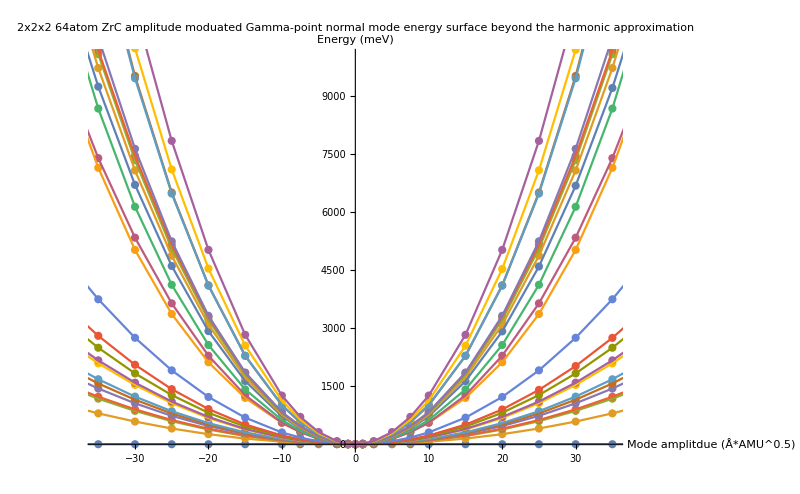

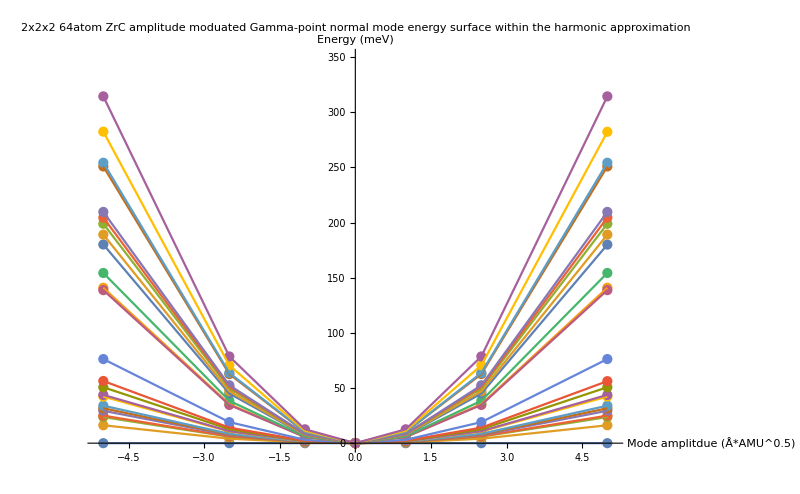

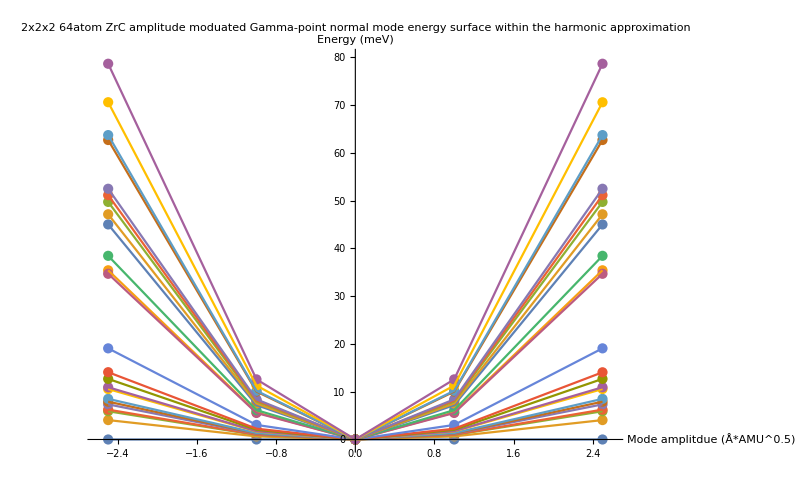

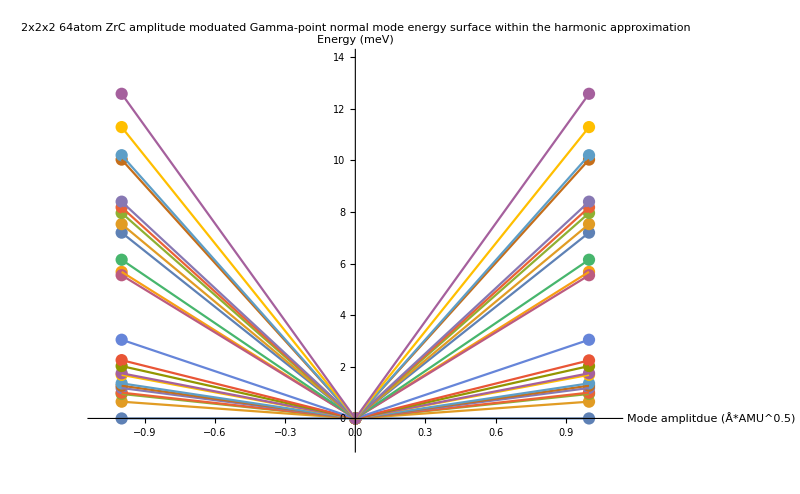

```mathematica
Plot modulated amplitude phonon potentials;
plotdata=Table[Transpose@{Flatten@Transpose[data][[1]],Flatten@Transpose[data][[i]]},{i,2,25}];
energysurfaceplot=ListPlot@plotdata;
energysurfaceplotjoined=ListPlot[plotdata,Joined->True];

plotinfo={ImageSize->800,PlotLabel->"2x2x2 64atom ZrC amplitude moduated Gamma-point normal mode energy surface beyond the harmonic approximation",AxesLabel->{"Mode amplitdue \n(Å*AMU^0.5)","Energy (meV)"},PlotRange->{{-35,35},{-1,10000}}};
Show[energysurfaceplot,energysurfaceplotjoined,plotinfo]



plotinfoHarmonic3={ImageSize->800,PlotLabel->"2x2x2 64atom ZrC amplitude moduated Gamma-point normal mode energy surface within the harmonic approximation",AxesLabel->{"Mode amplitdue \n(Å*AMU^0.5)","Energy (meV)"},PlotRange->{{-5.1,5.1},{-1,350}}};
plotdataHarmonic3=Table[Transpose@{Flatten@Transpose[dataHarmonic3][[1]],Flatten@Transpose[dataHarmonic3][[i]]},{i,2,25}];

energysurfaceplotHarmonic3=ListPlot[plotdataHarmonic3,plotinfoHarmonic3];
energysurfaceplotjoinedHarmonic3=ListPlot[plotdataHarmonic3,Joined->True,plotinfoHarmonic3];
Show[energysurfaceplotHarmonic3,energysurfaceplotjoinedHarmonic3,plotinfoHarmonic3]

plotinfoHarmonic2={ImageSize->800,PlotLabel->"2x2x2 64atom ZrC amplitude moduated Gamma-point normal mode energy surface within the harmonic approximation",AxesLabel->{"Mode amplitdue \n(Å*AMU^0.5)","Energy (meV)"},PlotRange->{{-2.6,2.6},{-1,80}}};
plotdataHarmonic2=Table[Transpose@{Flatten@Transpose[dataHarmonic2][[1]],Flatten@Transpose[dataHarmonic2][[i]]},{i,2,25}];

energysurfaceplotHarmonic2=ListPlot[plotdataHarmonic2,plotinfoHarmonic2];
energysurfaceplotjoinedHarmonic2=ListPlot[plotdataHarmonic2,Joined->True,plotinfoHarmonic2];
Show[energysurfaceplotHarmonic2,energysurfaceplotjoinedHarmonic2,plotinfoHarmonic2]

plotinfoHarmonic1={ImageSize->800,PlotLabel->"2x2x2 64atom ZrC amplitude moduated Gamma-point normal mode energy surface within the harmonic approximation",AxesLabel->{"Mode amplitdue \n(Å*AMU^0.5)","Energy (meV)"},PlotRange->{{-1.1,1.1},{-1,14}}};
plotdataHarmonic1=Table[Transpose@{Flatten@Transpose[dataHarmonic1][[1]],Flatten@Transpose[dataHarmonic1][[i]]},{i,2,25}];

energysurfaceplotHarmonic1=ListPlot[plotdataHarmonic1,plotinfoHarmonic1];
energysurfaceplotjoinedHarmonic1=ListPlot[plotdataHarmonic1,Joined->True,plotinfoHarmonic1];
Show[energysurfaceplotHarmonic1,energysurfaceplotjoinedHarmonic1,plotinfoHarmonic1]
```

```mathematica
Fit data to polynomial functions;
(*24 bands - 24 fits*)
(*Data format example*)
plotdata[[2]]//TableForm;
(*Fit all 24 bands - assume symmetry - note - is symmetry assumption valid - probably not in general but maybe for Gamma...*)

(*Define harmonic potential based on data set in the harmonic limit*)
UHarm[3,2,x_]:=Table[Fit[plotdataHarmonic3[[i]],{x^2},x],{i,1,24}];
UHarm[2,2,x_]:=Table[Fit[plotdataHarmonic2[[i]],{x^2},x],{i,1,24}];
UHarm[1,2,x_]:=Table[Fit[plotdataHarmonic1[[i]],{x^2},x],{i,1,24}];

(*Define potentials from 2nd to 12th order based on the full data set*)
U[2,x_]:=Table[Fit[plotdata[[i]],{x^2},x],{i,1,24}];
U[4,x_]:=Table[Fit[plotdata[[i]],{x^2,x^4},x],{i,1,24}];
U[6,x_]:=Table[Fit[plotdata[[i]],{x^2,x^4,x^6},x],{i,1,24}];
U[8,x_]:=Table[Fit[plotdata[[i]],{x^2,x^4,x^6,x^8},x],{i,1,24}];
U[10,x_]:=Table[Fit[plotdata[[i]],{x^2,x^4,x^6,x^8,x^10},x],{i,1,24}];
U[12,x_]:=Table[Fit[plotdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,24}];
```

```mathematica
Plot fits for Zr and C potentials;
plotlegend={PlotLegends->SwatchLegend[{"2nd 3point","2nd 5point","2nd 7point","2nd 27point","6th 27point","12th 27point"}],PlotLabel->"Phonon potential",AxesLabel->{"Mode amplitude\n (Ang*amu^0.5)|","Energy (meV/atom)"},ImageSize->500};
(*Plot 2nd, 6th and 12th order fits for 2nd (2/24) band*)
(*2nd band - mixed character Zr and C*)
plot1=Plot[Evaluate@{UHarm[3,2,x][[2]],UHarm[2,2,x][[2]],UHarm[1,2,x][[2]],U[2,x][[2]],U[6,x][[2]],U[12,x][[2]]},{x,-10,10},Evaluate@plotlegend];
plot2=Plot[Evaluate@{UHarm[3,2,x][[2]],UHarm[2,2,x][[2]],UHarm[1,2,x][[2]],U[2,x][[2]],U[6,x][[2]],U[12,x][[2]]},{x,-30,30},Evaluate@plotlegend];
plot3=Plot[Evaluate@{UHarm[3,2,x][[2]],UHarm[2,2,x][[2]],UHarm[1,2,x][[2]],U[2,x][[2]],U[6,x][[2]],U[12,x][[2]]},{x,-50,50},Evaluate@plotlegend];

GraphicsGrid[{{plot1,plot2,plot3}},ImageSize->1900]

(*primarily a Zr band*)
plot4=Plot[Evaluate@{UHarm[3,2,x][[10]],UHarm[2,2,x][[10]],UHarm[1,2,x][[10]],U[2,x][[10]],U[6,x][[10]],U[12,x][[10]]},{x,-10,10},Evaluate@plotlegend];
plot5=Plot[Evaluate@{UHarm[3,2,x][[10]],UHarm[2,2,x][[10]],UHarm[1,2,x][[10]],U[2,x][[10]],U[6,x][[10]],U[12,x][[10]]},{x,-30,30},Evaluate@plotlegend];
plot6=Plot[Evaluate@{UHarm[3,2,x][[10]],UHarm[2,2,x][[10]],UHarm[1,2,x][[10]],U[2,x][[10]],U[6,x][[10]],U[12,x][[10]]},{x,-50,50},Evaluate@plotlegend];
GraphicsGrid[{{plot4,plot5,plot6}},ImageSize->1900]

(*Mainly carbon band*)
plot7=Plot[Evaluate@{UHarm[3,2,x][[22]],UHarm[2,2,x][[22]],UHarm[1,2,x][[22]],U[2,x][[22]],U[6,x][[22]],U[12,x][[22]]},{x,-10,10},Evaluate@plotlegend];
plot8=Plot[Evaluate@{UHarm[3,2,x][[22]],UHarm[2,2,x][[22]],UHarm[1,2,x][[22]],U[2,x][[22]],U[6,x][[22]],U[12,x][[22]]},{x,-30,30},Evaluate@plotlegend];
plot9=Plot[Evaluate@{UHarm[3,2,x][[22]],UHarm[2,2,x][[22]],UHarm[1,2,x][[22]],U[2,x][[22]],U[6,x][[22]],U[12,x][[22]]},{x,-50,50},Evaluate@plotlegend];
GraphicsGrid[{{plot7,plot8,plot9}},ImageSize->1900]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Define Hamiltonian for 24 irrep phonon potentials - 12 Zr and 12 C  potentials or bands;
(*Definitions - hbar=1, mass in AMU*)
(*Notes - Vibrational Hamiltonian = -1/2 nabla + 1/2 omega*omega*q*q - given Hamiltonian form, mass wrapped up inside q*)

(*4th order Hamiltonian for all 24 bands*)
ℒ=Table[-(1/2)*u''[x]+U[4,x][[band]]*u[x],{band,1,24}];
(*1 point harmonic Hamiltonian for all 24 bands*)
ℒHarm=Table[-(1/2)*u''[x]+UHarm[1,2,x][[band]]*u[x],{band,1,24}];
(*2nd,4th,6th,8th,10th and 12th order Hamiltonians for all 24 bands*)
ℒal=Table[Table[-(1/2)*u''[x]+U[2*order,x][[band]]*u[x],{band,1,24}],{order,1,6}];

(*Hamiltonian for 4th band (a Zr band) for symmetric potential up to 12th order*)
"4th band (Zirconium mainly) Hamiltonians up to 12th order fitted on full data set"
Flatten[{ℒHarm[[4]],Table[ℒal[[i]][[4]],{i,1,6}]}]//TableForm
"4th band (Zirconium mainly) harmonic  Hamiltonian  fitted on harmonic only data set"
ℒHarm[[4]]

(*Hamiltonian for 24th band (a Zr band) for symmetric potential up to 12th order*)
"24th band (Carbon mainly) Hamiltonians up to 12th order"
Table[ℒal[[i]][[24]],{i,1,6}]//TableForm
"4th band (Zirconium mainly) harmonic  Hamiltonian  fitted on harmonic only data set"
ℒHarm[[24]]

(*Clearly the aharmonicity is larger for the higher bands dominated by the lighter atom, Carbon*)
```

4th band (Zirconium mainly) Hamiltonians up to 12th order fitted on full data set

1. x^2 u[x]-u''[x]/2
1.00308 x^2 u[x]-u''[x]/2
(0.998429 x^2+2.38276×10^-6 x^4) u[x]-u''[x]/2
(0.998901 x^2+1.74897×10^-6 x^4+1.84868×10^-10 x^6) u[x]-u''[x]/2
(0.998876 x^2+1.8127×10^-6 x^4+1.39746×10^-10 x^6+9.50733×10^-15 x^8) u[x]-u''[x]/2
(0.998613 x^2+2.91152×10^-6 x^4-1.25882×10^-9 x^6+7.01372×10^-13 x^8-1.16602×10^-16 x^10) u[x]-u''[x]/2
(0.998593 x^2+3.04049×10^-6 x^4-1.5203×10^-9 x^6+9.28808×10^-13 x^8-2.05182×10^-16 x^10+1.2682×10^-20 x^12) u[x]-u''[x]/2

4th band (Zirconium mainly) harmonic  Hamiltonian  fitted on harmonic only data set

1. x^2 u[x]-u''[x]/2

24th band (Carbon mainly) Hamiltonians up to 12th order

12.4474 x^2 u[x]-u''[x]/2
(12.5916 x^2-0.000073876 x^4) u[x]-u''[x]/2
(12.5739 x^2-0.000050187 x^4-6.9097×10^-9 x^6) u[x]-u''[x]/2
(12.5765 x^2-0.0000565766 x^4-2.3862×10^-9 x^6-9.53108×10^-13 x^8) u[x]-u''[x]/2
(12.5794 x^2-0.0000688651 x^4+1.32545×10^-8 x^6-8.69047×10^-12 x^8+1.304×10^-15 x^10) u[x]-u''[x]/2
(12.5779 x^2-0.0000594509 x^4-5.83233×10^-9 x^6+7.91152×10^-12 x^8-5.16206×10^-15 x^10+9.25737×10^-19 x^12) u[x]-u''[x]/2

4th band (Zirconium mainly) harmonic  Hamiltonian  fitted on harmonic only data set

12.58 x^2 u[x]-u''[x]/2

```mathematica
Solve Hamiltonians for 2nd and12th order fits for the first 10 eigenvalues of all 24 bands;
```

```mathematica
maxBand=24;
maxEigenval=40;
```

```mathematica
ℒHarm
```

{0.-u''[x]/2,0.65 x^2 u[x]-u''[x]/2,0.95 x^2 u[x]-u''[x]/2,1. x^2 u[x]-u''[x]/2,1.18 x^2 u[x]-u''[x]/2,1.27 x^2 u[x]-u''[x]/2,1.36 x^2 u[x]-u''[x]/2,1.69 x^2 u[x]-u''[x]/2,1.75 x^2 u[x]-u''[x]/2,2.03 x^2 u[x]-u''[x]/2,2.255 x^2 u[x]-u''[x]/2,3.05 x^2 u[x]-u''[x]/2,5.68 x^2 u[x]-u''[x]/2,5.55 x^2 u[x]-u''[x]/2,6.15 x^2 u[x]-u''[x]/2,7.2 x^2 u[x]-u''[x]/2,7.53 x^2 u[x]-u''[x]/2,7.96 x^2 u[x]-u''[x]/2,8.18 x^2 u[x]-u''[x]/2,8.4 x^2 u[x]-u''[x]/2,10.03 x^2 u[x]-u''[x]/2,10.2 x^2 u[x]-u''[x]/2,11.29 x^2 u[x]-u''[x]/2,12.58 x^2 u[x]-u''[x]/2}

```mathematica
omega0Eigensystem=2*Table[NDEigensystem[ℒHarm[[bands]],u[x],{x,-10,10},1
,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}],{bands,1,maxBand}];
(*Within the harmonic approximation fitted on a single data point at the 60th eigenvalue the 24 bands have a range spanning 9 to 600meV*)
(*Since the at the 60th eigenvalue the biggest band energy is only 600meV mode amplitude bounds of plus and minus 10 are sufficient to solve the eigen problem*)
```

```mathematica
(*Be careful - this a long time to evaulate *)
(*omega0Eigensystem=Table[2*Table[NDEigensystem[ℒal[[order]][[bands]],u[x],{x,-10,10},1,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}],{bands,1,maxBand}],{order,1,6,5}];*)

fullEigensystem=Table[Table[NDEigensystem[ℒal[[order]][[bands]],u[x],{x,-10,10},maxEigenval,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}],{bands,1,maxBand}],{order,1,6,5}];
```

```mathematica
Extract  omega0 and the full spectrum of eigenvalues for the 2nd and 12th order fits;
(*old: omega0EigenValues=Table[Transpose[omega0Eigensystem[[order]]][[1]],{order,1,2,1}];*)
omega0EigenValues=Transpose[omega0Eigensystem][[1]];
fullEigenValues=Table[Transpose[fullEigensystem[[order]]][[1]],{order,1,2,1}];
```

```mathematica
omega0EigenValues[[5]]
```

{1.53623}

```mathematica
Examine the first 10 eigenvalues of the 12 lowest bands - ie the Zr dominated bands - for 2nd and 12th order fits;
localmaxband=12;
bands={"Bands",1,2,3,4,5,6,7,8,9,10,11,12};

namelist={"1st eigenvalue","2nd eigenvalue","3rd eigenvalue","4th eigenvalue","5th eigenvalue","6th eigenvalue" ,"7th eigenvalue","8th eigenvalue","9th eigenvalue","10th eigenvalue","11th eigenvalue","12th eigenvalue","13th eigenvalue","14th eigenvalue","15th eigenvalue","16th eigenvalue" ,"17th eigenvalue","18th eigenvalue","19th eigenvalue","20th eigenvalue","21st eigenvalue","22nd eigenvalue","23rd eigenvalue","24th eigenvalue","25th eigenvalue","26th eigenvalue" ,"27th eigenvalue","28th eigenvalue","29th eigenvalue","30th eigenvalue","31st eigenvalue","32nd eigenvalue","33rd eigenvalue","34th eigenvalue","35th eigenvalue","36th eigenvalue" ,"37th eigenvalue","38th eigenvalue","39th eigenvalue","40th eigenvalue"};

"Zirconium: (2nd-order fit - all data) / (2nd-order fit - harmonic limit)"
Table[{namelist,{Table[Flatten@{{fullEigenValues[[order]][[bands]]/omega0EigenValues[[bands]][[1]]}},{bands,1,localmaxband}]}},{order,1,1}];
Partition[Flatten[%],40]//TableForm

"Zironcium: 12th order fit eigenvalues/harmonic_omega0 ie (12th-order fit - all data) / (2nd-order fit - harmonic limit):"
Table[{namelist,{Table[Flatten@{{fullEigenValues[[order]][[bands]]/omega0EigenValues[[bands]][[1]]}},{bands,1,localmaxband}]}},{order,2,2}];
Partition[Flatten[%],40]//TableForm
```

Zirconium: (2nd-order fit - all data) / (2nd-order fit - harmonic limit)

1st eigenvalue | 2nd eigenvalue | 3rd eigenvalue | 4th eigenvalue | 5th eigenvalue | 6th eigenvalue | 7th eigenvalue | 8th eigenvalue | 9th eigenvalue | 10th eigenvalue | 11th eigenvalue | 12th eigenvalue | 13th eigenvalue | 14th eigenvalue | 15th eigenvalue | 16th eigenvalue | 17th eigenvalue | 18th eigenvalue | 19th eigenvalue | 20th eigenvalue | 21st eigenvalue | 22nd eigenvalue | 23rd eigenvalue | 24th eigenvalue | 25th eigenvalue | 26th eigenvalue | 27th eigenvalue | 28th eigenvalue | 29th eigenvalue | 30th eigenvalue | 31st eigenvalue | 32nd eigenvalue | 33rd eigenvalue | 34th eigenvalue | 35th eigenvalue | 36th eigenvalue | 37th eigenvalue | 38th eigenvalue | 39th eigenvalue | 40th eigenvalue
0.5 | 4.45081×10^7 | 1.78032×10^8 | 4.00573×10^8 | 7.12129×10^8 | 1.1127×10^9 | 1.60229×10^9 | 2.1809×10^9 | 2.84852×10^9 | 3.60516×10^9 | 4.45081×10^9 | 5.38548×10^9 | 6.40916×10^9 | 7.52187×10^9 | 8.72359×10^9 | 1.00143×10^10 | 1.13941×10^10 | 1.28628×10^10 | 1.44206×10^10 | 1.60674×10^10 | 1.78032×10^10 | 1.96281×10^10 | 2.15419×10^10 | 2.35448×10^10 | 2.56367×10^10 | 2.78176×10^10 | 3.00875×10^10 | 3.24464×10^10 | 3.48943×10^10 | 3.74313×10^10 | 4.00573×10^10 | 4.27723×10^10 | 4.55763×10^10 | 4.84693×10^10 | 5.14514×10^10 | 5.45224×10^10 | 5.76825×10^10 | 6.09316×10^10 | 6.42697×10^10 | 6.76968×10^10
0.500775 | 1.50232 | 2.50387 | 3.50542 | 4.50697 | 5.50852 | 6.51007 | 7.51162 | 8.51317 | 9.51472 | 10.5163 | 11.5178 | 12.5194 | 13.5209 | 14.5225 | 15.524 | 16.5256 | 17.5271 | 18.5287 | 19.5302 | 20.5318 | 21.5333 | 22.5349 | 23.5364 | 24.538 | 25.5395 | 26.5411 | 27.5426 | 28.5442 | 29.5457 | 30.5473 | 31.5488 | 32.5504 | 33.5519 | 34.5535 | 35.555 | 36.5566 | 37.5581 | 38.5597 | 39.5612
0.504913 | 1.51474 | 2.52456 | 3.53439 | 4.54422 | 5.55404 | 6.56387 | 7.57369 | 8.58352 | 9.59334 | 10.6032 | 11.613 | 12.6228 | 13.6326 | 14.6425 | 15.6523 | 16.6621 | 17.6719 | 18.6818 | 19.6916 | 20.7014 | 21.7113 | 22.7211 | 23.7309 | 24.7407 | 25.7506 | 26.7604 | 27.7702 | 28.78 | 29.7899 | 30.7997 | 31.8095 | 32.8193 | 33.8292 | 34.839 | 35.8488 | 36.8586 | 37.8685 | 38.8783 | 39.8881
0.500769 | 1.50231 | 2.50385 | 3.50539 | 4.50693 | 5.50846 | 6.51 | 7.51154 | 8.51308 | 9.51462 | 10.5162 | 11.5177 | 12.5192 | 13.5208 | 14.5223 | 15.5239 | 16.5254 | 17.5269 | 18.5285 | 19.53 | 20.5315 | 21.5331 | 22.5346 | 23.5362 | 24.5377 | 25.5392 | 26.5408 | 27.5423 | 28.5439 | 29.5454 | 30.5469 | 31.5485 | 32.55 | 33.5516 | 34.5531 | 35.5546 | 36.5562 | 37.5577 | 38.5593 | 39.5608
0.499106 | 1.49732 | 2.49553 | 3.49374 | 4.49196 | 5.49017 | 6.48838 | 7.48659 | 8.48481 | 9.48302 | 10.4812 | 11.4794 | 12.4777 | 13.4759 | 14.4741 | 15.4723 | 16.4705 | 17.4687 | 18.4669 | 19.4651 | 20.4634 | 21.4616 | 22.4598 | 23.458 | 24.4562 | 25.4544 | 26.4526 | 27.4508 | 28.4491 | 29.4473 | 30.4455 | 31.4437 | 32.4419 | 33.4401 | 34.4383 | 35.4365 | 36.4348 | 37.433 | 38.4312 | 39.4294
0.503792 | 1.51138 | 2.51896 | 3.52655 | 4.53413 | 5.54172 | 6.5493 | 7.55688 | 8.56447 | 9.57205 | 10.5796 | 11.5872 | 12.5948 | 13.6024 | 14.61 | 15.6176 | 16.6251 | 17.6327 | 18.6403 | 19.6479 | 20.6555 | 21.6631 | 22.6707 | 23.6782 | 24.6858 | 25.6934 | 26.701 | 27.7086 | 28.7162 | 29.7237 | 30.7313 | 31.7389 | 32.7465 | 33.7541 | 34.7617 | 35.7693 | 36.7768 | 37.7844 | 38.792 | 39.7996
0.503238 | 1.50971 | 2.51619 | 3.52267 | 4.52914 | 5.53562 | 6.54209 | 7.54857 | 8.55505 | 9.56152 | 10.568 | 11.5745 | 12.5809 | 13.5874 | 14.5939 | 15.6004 | 16.6069 | 17.6133 | 18.6198 | 19.6263 | 20.6328 | 21.6392 | 22.6457 | 23.6522 | 24.6587 | 25.6651 | 26.6716 | 27.6781 | 28.6846 | 29.691 | 30.6975 | 31.704 | 32.7105 | 33.7169 | 34.7234 | 35.7299 | 36.7364 | 37.7428 | 38.7493 | 39.7558
0.503616 | 1.51085 | 2.51808 | 3.52531 | 4.53255 | 5.53978 | 6.54701 | 7.55425 | 8.56148 | 9.56871 | 10.5759 | 11.5832 | 12.5904 | 13.5976 | 14.6049 | 15.6121 | 16.6193 | 17.6266 | 18.6338 | 19.641 | 20.6483 | 21.6555 | 22.6627 | 23.67 | 24.6772 | 25.6844 | 26.6917 | 27.6989 | 28.7061 | 29.7134 | 30.7206 | 31.7278 | 32.7351 | 33.7423 | 34.7495 | 35.7568 | 36.764 | 37.7712 | 38.7785 | 39.7857
0.503171 | 1.50951 | 2.51586 | 3.5222 | 4.52854 | 5.53488 | 6.54123 | 7.54757 | 8.55391 | 9.56025 | 10.5666 | 11.5729 | 12.5793 | 13.5856 | 14.592 | 15.5983 | 16.6046 | 17.611 | 18.6173 | 19.6237 | 20.63 | 21.6364 | 22.6427 | 23.649 | 24.6554 | 25.6617 | 26.6681 | 27.6744 | 28.6808 | 29.6871 | 30.6934 | 31.6998 | 32.7061 | 33.7125 | 34.7188 | 35.7252 | 36.7315 | 37.7378 | 38.7442 | 39.7505
0.501306 | 1.50392 | 2.50653 | 3.50914 | 4.51175 | 5.51436 | 6.51698 | 7.51959 | 8.5222 | 9.52481 | 10.5274 | 11.53 | 12.5326 | 13.5353 | 14.5379 | 15.5405 | 16.5431 | 17.5457 | 18.5483 | 19.5509 | 20.5535 | 21.5561 | 22.5588 | 23.5614 | 24.564 | 25.5666 | 26.5692 | 27.5718 | 28.5744 | 29.577 | 30.5797 | 31.5823 | 32.5849 | 33.5875 | 34.5901 | 35.5927 | 36.5953 | 37.5979 | 38.6005 | 39.6032
0.501418 | 1.50425 | 2.50709 | 3.50993 | 4.51276 | 5.5156 | 6.51844 | 7.52127 | 8.52411 | 9.52694 | 10.5298 | 11.5326 | 12.5355 | 13.5383 | 14.5411 | 15.544 | 16.5468 | 17.5496 | 18.5525 | 19.5553 | 20.5581 | 21.561 | 22.5638 | 23.5667 | 24.5695 | 25.5723 | 26.5752 | 27.578 | 28.5808 | 29.5837 | 30.5865 | 31.5893 | 32.5922 | 33.595 | 34.5979 | 35.6007 | 36.6035 | 37.6064 | 38.6092 | 39.612
0.50093 | 1.50279 | 2.50465 | 3.50651 | 4.50837 | 5.51023 | 6.51209 | 7.51395 | 8.51581 | 9.51767 | 10.5195 | 11.5214 | 12.5232 | 13.5251 | 14.527 | 15.5288 | 16.5307 | 17.5325 | 18.5344 | 19.5363 | 20.5381 | 21.54 | 22.5418 | 23.5437 | 24.5456 | 25.5474 | 26.5493 | 27.5511 | 28.553 | 29.5549 | 30.5567 | 31.5586 | 32.5604 | 33.5623 | 34.5642 | 35.566 | 36.5679 | 37.5697 | 38.5716 | 39.5734

Zironcium: 12th order fit eigenvalues/harmonic_omega0 ie (12th-order fit - all data) / (2nd-order fit - harmonic limit):

1st eigenvalue | 2nd eigenvalue | 3rd eigenvalue | 4th eigenvalue | 5th eigenvalue | 6th eigenvalue | 7th eigenvalue | 8th eigenvalue | 9th eigenvalue | 10th eigenvalue | 11th eigenvalue | 12th eigenvalue | 13th eigenvalue | 14th eigenvalue | 15th eigenvalue | 16th eigenvalue | 17th eigenvalue | 18th eigenvalue | 19th eigenvalue | 20th eigenvalue | 21st eigenvalue | 22nd eigenvalue | 23rd eigenvalue | 24th eigenvalue | 25th eigenvalue | 26th eigenvalue | 27th eigenvalue | 28th eigenvalue | 29th eigenvalue | 30th eigenvalue | 31st eigenvalue | 32nd eigenvalue | 33rd eigenvalue | 34th eigenvalue | 35th eigenvalue | 36th eigenvalue | 37th eigenvalue | 38th eigenvalue | 39th eigenvalue | 40th eigenvalue
0.5 | 4.45081×10^7 | 1.78032×10^8 | 4.00573×10^8 | 7.12129×10^8 | 1.1127×10^9 | 1.60229×10^9 | 2.1809×10^9 | 2.84852×10^9 | 3.60516×10^9 | 4.45081×10^9 | 5.38548×10^9 | 6.40916×10^9 | 7.52187×10^9 | 8.72359×10^9 | 1.00143×10^10 | 1.13941×10^10 | 1.28628×10^10 | 1.44206×10^10 | 1.60674×10^10 | 1.78032×10^10 | 1.96281×10^10 | 2.15419×10^10 | 2.35448×10^10 | 2.56367×10^10 | 2.78176×10^10 | 3.00875×10^10 | 3.24464×10^10 | 3.48943×10^10 | 3.74313×10^10 | 4.00573×10^10 | 4.27723×10^10 | 4.55763×10^10 | 4.84693×10^10 | 5.14514×10^10 | 5.45224×10^10 | 5.76825×10^10 | 6.09316×10^10 | 6.42697×10^10 | 6.76968×10^10
0.49958 | 1.49874 | 2.49791 | 3.49709 | 4.49627 | 5.49546 | 6.49466 | 7.49386 | 8.49307 | 9.49229 | 10.4915 | 11.4907 | 12.49 | 13.4892 | 14.4885 | 15.4877 | 16.487 | 17.4863 | 18.4855 | 19.4848 | 20.4841 | 21.4834 | 22.4827 | 23.482 | 24.4813 | 25.4806 | 26.48 | 27.4793 | 28.4786 | 29.478 | 30.4773 | 31.4767 | 32.476 | 33.4754 | 34.4748 | 35.4742 | 36.4735 | 37.4729 | 38.4723 | 39.4717
0.498789 | 1.49638 | 2.49398 | 3.49159 | 4.48922 | 5.48686 | 6.48452 | 7.4822 | 8.47988 | 9.47758 | 10.4753 | 11.473 | 12.4708 | 13.4685 | 14.4663 | 15.4641 | 16.4619 | 17.4597 | 18.4576 | 19.4554 | 20.4533 | 21.4511 | 22.449 | 23.4469 | 24.4448 | 25.4428 | 26.4407 | 27.4387 | 28.4367 | 29.4347 | 30.4327 | 31.4307 | 32.4287 | 33.4268 | 34.4248 | 35.4229 | 36.421 | 37.4191 | 38.4172 | 39.4153
0.499649 | 1.49895 | 2.49825 | 3.49756 | 4.49687 | 5.49618 | 6.49549 | 7.49481 | 8.49413 | 9.49346 | 10.4928 | 11.4921 | 12.4915 | 13.4908 | 14.4901 | 15.4895 | 16.4888 | 17.4882 | 18.4875 | 19.4869 | 20.4862 | 21.4856 | 22.485 | 23.4843 | 24.4837 | 25.4831 | 26.4825 | 27.4818 | 28.4812 | 29.4806 | 30.48 | 31.4794 | 32.4788 | 33.4782 | 34.4776 | 35.477 | 36.4764 | 37.4758 | 38.4752 | 39.4747
0.498949 | 1.49685 | 2.49474 | 3.49264 | 4.49053 | 5.48843 | 6.48632 | 7.48422 | 8.48211 | 9.48 | 10.4779 | 11.4758 | 12.4737 | 13.4716 | 14.4695 | 15.4673 | 16.4652 | 17.4631 | 18.461 | 19.4589 | 20.4568 | 21.4547 | 22.4526 | 23.4504 | 24.4483 | 25.4462 | 26.4441 | 27.442 | 28.4399 | 29.4377 | 30.4356 | 31.4335 | 32.4314 | 33.4293 | 34.4271 | 35.425 | 36.4229 | 37.4208 | 38.4186 | 39.4165
0.498998 | 1.497 | 2.495 | 3.49302 | 4.49105 | 5.48908 | 6.48712 | 7.48518 | 8.48324 | 9.4813 | 10.4794 | 11.4775 | 12.4756 | 13.4737 | 14.4718 | 15.4699 | 16.468 | 17.4662 | 18.4643 | 19.4625 | 20.4606 | 21.4588 | 22.457 | 23.4552 | 24.4534 | 25.4516 | 26.4498 | 27.4481 | 28.4463 | 29.4446 | 30.4428 | 31.4411 | 32.4394 | 33.4376 | 34.4359 | 35.4342 | 36.4326 | 37.4309 | 38.4292 | 39.4275
0.499926 | 1.49978 | 2.49964 | 3.49951 | 4.49938 | 5.49925 | 6.49913 | 7.49902 | 8.49891 | 9.4988 | 10.4987 | 11.4986 | 12.4985 | 13.4984 | 14.4983 | 15.4983 | 16.4982 | 17.4981 | 18.4981 | 19.498 | 20.498 | 21.4979 | 22.4979 | 23.4978 | 24.4978 | 25.4978 | 26.4978 | 27.4977 | 28.4977 | 29.4977 | 30.4977 | 31.4977 | 32.4977 | 33.4977 | 34.4978 | 35.4978 | 36.4978 | 37.4978 | 38.4979 | 39.4979
0.499915 | 1.49975 | 2.49959 | 3.49944 | 4.49929 | 5.49915 | 6.49902 | 7.4989 | 8.49878 | 9.49867 | 10.4986 | 11.4985 | 12.4984 | 13.4983 | 14.4982 | 15.4982 | 16.4981 | 17.498 | 18.498 | 19.498 | 20.4979 | 21.4979 | 22.4979 | 23.4979 | 24.4979 | 25.4979 | 26.4979 | 27.4979 | 28.4979 | 29.4979 | 30.498 | 31.498 | 32.4981 | 33.4981 | 34.4982 | 35.4983 | 36.4984 | 37.4984 | 38.4985 | 39.4986
0.499822 | 1.49948 | 2.49915 | 3.49884 | 4.49856 | 5.49829 | 6.49804 | 7.49781 | 8.4976 | 9.4974 | 10.4972 | 11.4971 | 12.4969 | 13.4968 | 14.4967 | 15.4966 | 16.4966 | 17.4965 | 18.4965 | 19.4965 | 20.4965 | 21.4966 | 22.4966 | 23.4967 | 24.4968 | 25.4969 | 26.497 | 27.4971 | 28.4973 | 29.4975 | 30.4977 | 31.4979 | 32.4981 | 33.4983 | 34.4986 | 35.4989 | 36.4992 | 37.4995 | 38.4998 | 39.5002
0.499797 | 1.49939 | 2.49899 | 3.49859 | 4.4982 | 5.4978 | 6.49741 | 7.49702 | 8.49664 | 9.49625 | 10.4959 | 11.4955 | 12.4951 | 13.4947 | 14.4944 | 15.494 | 16.4936 | 17.4933 | 18.4929 | 19.4926 | 20.4922 | 21.4918 | 22.4915 | 23.4911 | 24.4908 | 25.4904 | 26.4901 | 27.4898 | 28.4894 | 29.4891 | 30.4888 | 31.4884 | 32.4881 | 33.4878 | 34.4875 | 35.4871 | 36.4868 | 37.4865 | 38.4862 | 39.4859
0.499455 | 1.49837 | 2.49729 | 3.49622 | 4.49516 | 5.49411 | 6.49306 | 7.49202 | 8.491 | 9.48998 | 10.489 | 11.488 | 12.487 | 13.486 | 14.485 | 15.484 | 16.4831 | 17.4821 | 18.4812 | 19.4802 | 20.4793 | 21.4784 | 22.4774 | 23.4765 | 24.4756 | 25.4747 | 26.4739 | 27.473 | 28.4721 | 29.4713 | 30.4704 | 31.4696 | 32.4687 | 33.4679 | 34.4671 | 35.4663 | 36.4655 | 37.4647 | 38.4639 | 39.4631
0.499954 | 1.49986 | 2.49977 | 3.49969 | 4.4996 | 5.49952 | 6.49943 | 7.49935 | 8.49927 | 9.49919 | 10.4991 | 11.499 | 12.499 | 13.4989 | 14.4988 | 15.4988 | 16.4987 | 17.4986 | 18.4986 | 19.4985 | 20.4984 | 21.4984 | 22.4983 | 23.4983 | 24.4982 | 25.4982 | 26.4981 | 27.4981 | 28.498 | 29.498 | 30.4979 | 31.4979 | 32.4978 | 33.4978 | 34.4978 | 35.4977 | 36.4977 | 37.4977 | 38.4976 | 39.4976

```mathematica
Examine the first 10 eigenvalues of the 12 highest bands - ie the C dominated bands - for 2nd and 12th order fits;
```

```mathematica
localmaxband=24;
localminband=13;

"Carbon: (2nd-order fit - all data) / (2nd-order fit - harmonic limit)"
Table[{namelist,{Table[Flatten@{{fullEigenValues[[order]][[bands]]/omega0EigenValues[[bands]][[1]]}},{bands,localminband,localmaxband}]}},{order,1,1}];
Partition[Flatten[%],maxEigenval]//TableForm

"Carbon: 12th order fit eigenvalues/harmonic_omega0 ie (12th-order fit - all data) / (2nd-order fit - harmonic limit):"
Table[{namelist,{Table[Flatten@{{fullEigenValues[[order]][[bands]]/omega0EigenValues[[bands]][[1]]}},{bands,localminband,localmaxband}]}},{order,2,2}];
Partition[Flatten[%],maxEigenval]//TableForm
```

Carbon: (2nd-order fit - all data) / (2nd-order fit - harmonic limit)

1st eigenvalue | 2nd eigenvalue | 3rd eigenvalue | 4th eigenvalue | 5th eigenvalue | 6th eigenvalue | 7th eigenvalue | 8th eigenvalue | 9th eigenvalue | 10th eigenvalue | 11th eigenvalue | 12th eigenvalue | 13th eigenvalue | 14th eigenvalue | 15th eigenvalue | 16th eigenvalue | 17th eigenvalue | 18th eigenvalue | 19th eigenvalue | 20th eigenvalue | 21st eigenvalue | 22nd eigenvalue | 23rd eigenvalue | 24th eigenvalue | 25th eigenvalue | 26th eigenvalue | 27th eigenvalue | 28th eigenvalue | 29th eigenvalue | 30th eigenvalue | 31st eigenvalue | 32nd eigenvalue | 33rd eigenvalue | 34th eigenvalue | 35th eigenvalue | 36th eigenvalue | 37th eigenvalue | 38th eigenvalue | 39th eigenvalue | 40th eigenvalue
0.525808 | 1.57742 | 2.62904 | 3.68066 | 4.73227 | 5.78389 | 6.8355 | 7.88712 | 8.93873 | 9.99035 | 11.042 | 12.0936 | 13.1452 | 14.1968 | 15.2484 | 16.3 | 17.3517 | 18.4033 | 19.4549 | 20.5065 | 21.5581 | 22.6097 | 23.6614 | 24.713 | 25.7646 | 26.8162 | 27.8678 | 28.9194 | 29.971 | 31.0227 | 32.0743 | 33.1259 | 34.1775 | 35.2291 | 36.2807 | 37.3324 | 38.384 | 39.4356 | 40.4872 | 41.5388
0.529407 | 1.58822 | 2.64704 | 3.70585 | 4.76467 | 5.82348 | 6.8823 | 7.94111 | 8.99993 | 10.0587 | 11.1176 | 12.1764 | 13.2352 | 14.294 | 15.3528 | 16.4116 | 17.4704 | 18.5293 | 19.5881 | 20.6469 | 21.7057 | 22.7645 | 23.8233 | 24.8821 | 25.941 | 26.9998 | 28.0586 | 29.1174 | 30.1762 | 31.235 | 32.2939 | 33.3527 | 34.4115 | 35.4703 | 36.5291 | 37.5879 | 38.6467 | 39.7056 | 40.7644 | 41.8232
0.557582 | 1.67275 | 2.78791 | 3.90307 | 5.01824 | 6.1334 | 7.24857 | 8.36373 | 9.47889 | 10.5941 | 11.7092 | 12.8244 | 13.9395 | 15.0547 | 16.1699 | 17.285 | 18.4002 | 19.5154 | 20.6305 | 21.7457 | 22.8609 | 23.976 | 25.0912 | 26.2064 | 27.3215 | 28.4367 | 29.5518 | 30.667 | 31.7822 | 32.8973 | 34.0125 | 35.1277 | 36.2428 | 37.358 | 38.4732 | 39.5883 | 40.7035 | 41.8186 | 42.9338 | 44.049
0.518684 | 1.55605 | 2.59342 | 3.63079 | 4.66815 | 5.70552 | 6.74289 | 7.78025 | 8.81762 | 9.85499 | 10.8924 | 11.9297 | 12.9671 | 14.0045 | 15.0418 | 16.0792 | 17.1166 | 18.1539 | 19.1913 | 20.2287 | 21.266 | 22.3034 | 23.3408 | 24.3781 | 25.4155 | 26.4529 | 27.4902 | 28.5276 | 29.565 | 30.6023 | 31.6397 | 32.6771 | 33.7144 | 34.7518 | 35.7892 | 36.8265 | 37.8639 | 38.9013 | 39.9386 | 40.976
0.518025 | 1.55407 | 2.59012 | 3.62617 | 4.66222 | 5.69827 | 6.73432 | 7.77037 | 8.80642 | 9.84247 | 10.8785 | 11.9146 | 12.9506 | 13.9867 | 15.0227 | 16.0588 | 17.0948 | 18.1309 | 19.1669 | 20.203 | 21.239 | 22.2751 | 23.3111 | 24.3472 | 25.3832 | 26.4193 | 27.4553 | 28.4914 | 29.5274 | 30.5635 | 31.5995 | 32.6356 | 33.6716 | 34.7077 | 35.7437 | 36.7798 | 37.8158 | 38.8519 | 39.8879 | 40.924
0.513232 | 1.5397 | 2.56616 | 3.59262 | 4.61909 | 5.64555 | 6.67201 | 7.69848 | 8.72494 | 9.75141 | 10.7779 | 11.8043 | 12.8308 | 13.8573 | 14.8837 | 15.9102 | 16.9367 | 17.9631 | 18.9896 | 20.016 | 21.0425 | 22.069 | 23.0954 | 24.1219 | 25.1484 | 26.1748 | 27.2013 | 28.2278 | 29.2542 | 30.2807 | 31.3071 | 32.3336 | 33.3601 | 34.3865 | 35.413 | 36.4395 | 37.4659 | 38.4924 | 39.5189 | 40.5453
0.505804 | 1.51741 | 2.52902 | 3.54063 | 4.55224 | 5.56384 | 6.57545 | 7.58706 | 8.59867 | 9.61028 | 10.6219 | 11.6335 | 12.6451 | 13.6567 | 14.6683 | 15.6799 | 16.6915 | 17.7031 | 18.7147 | 19.7264 | 20.738 | 21.7496 | 22.7612 | 23.7728 | 24.7844 | 25.796 | 26.8076 | 27.8192 | 28.8308 | 29.8424 | 30.854 | 31.8657 | 32.8773 | 33.8889 | 34.9005 | 35.9121 | 36.9237 | 37.9353 | 38.9469 | 39.9585
0.510832 | 1.5325 | 2.55416 | 3.57583 | 4.59749 | 5.61915 | 6.64082 | 7.66248 | 8.68415 | 9.70581 | 10.7275 | 11.7491 | 12.7708 | 13.7925 | 14.8141 | 15.8358 | 16.8575 | 17.8791 | 18.9008 | 19.9225 | 20.9441 | 21.9658 | 22.9874 | 24.0091 | 25.0308 | 26.0524 | 27.0741 | 28.0958 | 29.1174 | 30.1391 | 31.1608 | 32.1824 | 33.2041 | 34.2258 | 35.2474 | 36.2691 | 37.2908 | 38.3124 | 39.3341 | 40.3557
0.527938 | 1.58381 | 2.63969 | 3.69557 | 4.75144 | 5.80732 | 6.8632 | 7.91907 | 8.97495 | 10.0308 | 11.0867 | 12.1426 | 13.1985 | 14.2543 | 15.3102 | 16.3661 | 17.422 | 18.4778 | 19.5337 | 20.5896 | 21.6455 | 22.7013 | 23.7572 | 24.8131 | 25.869 | 26.9248 | 27.9807 | 29.0366 | 30.0925 | 31.1483 | 32.2042 | 33.2601 | 34.316 | 35.3719 | 36.4277 | 37.4836 | 38.5395 | 39.5954 | 40.6512 | 41.7071
0.519988 | 1.55996 | 2.59994 | 3.63992 | 4.67989 | 5.71987 | 6.75984 | 7.79982 | 8.8398 | 9.87977 | 10.9197 | 11.9597 | 12.9997 | 14.0397 | 15.0797 | 16.1196 | 17.1596 | 18.1996 | 19.2396 | 20.2795 | 21.3195 | 22.3595 | 23.3995 | 24.4394 | 25.4794 | 26.5194 | 27.5594 | 28.5993 | 29.6393 | 30.6793 | 31.7193 | 32.7592 | 33.7992 | 34.8392 | 35.8792 | 36.9191 | 37.9591 | 38.9991 | 40.0391 | 41.0791
0.501004 | 1.50301 | 2.50502 | 3.50703 | 4.50903 | 5.51104 | 6.51305 | 7.51506 | 8.51706 | 9.51907 | 10.5211 | 11.5231 | 12.5251 | 13.5271 | 14.5291 | 15.5311 | 16.5331 | 17.5351 | 18.5371 | 19.5391 | 20.5412 | 21.5432 | 22.5452 | 23.5472 | 24.5492 | 25.5512 | 26.5532 | 27.5552 | 28.5572 | 29.5592 | 30.5612 | 31.5632 | 32.5652 | 33.5672 | 34.5693 | 35.5713 | 36.5733 | 37.5753 | 38.5773 | 39.5793
0.497358 | 1.49207 | 2.48679 | 3.4815 | 4.47622 | 5.47093 | 6.46565 | 7.46036 | 8.45508 | 9.44979 | 10.4445 | 11.4392 | 12.4339 | 13.4287 | 14.4234 | 15.4181 | 16.4128 | 17.4075 | 18.4022 | 19.3969 | 20.3917 | 21.3864 | 22.3811 | 23.3758 | 24.3705 | 25.3652 | 26.36 | 27.3547 | 28.3494 | 29.3441 | 30.3388 | 31.3335 | 32.3282 | 33.323 | 34.3177 | 35.3124 | 36.3071 | 37.3018 | 38.2965 | 39.2913

Carbon: 12th order fit eigenvalues/harmonic_omega0 ie (12th-order fit - all data) / (2nd-order fit - harmonic limit):

1st eigenvalue | 2nd eigenvalue | 3rd eigenvalue | 4th eigenvalue | 5th eigenvalue | 6th eigenvalue | 7th eigenvalue | 8th eigenvalue | 9th eigenvalue | 10th eigenvalue | 11th eigenvalue | 12th eigenvalue | 13th eigenvalue | 14th eigenvalue | 15th eigenvalue | 16th eigenvalue | 17th eigenvalue | 18th eigenvalue | 19th eigenvalue | 20th eigenvalue | 21st eigenvalue | 22nd eigenvalue | 23rd eigenvalue | 24th eigenvalue | 25th eigenvalue | 26th eigenvalue | 27th eigenvalue | 28th eigenvalue | 29th eigenvalue | 30th eigenvalue | 31st eigenvalue | 32nd eigenvalue | 33rd eigenvalue | 34th eigenvalue | 35th eigenvalue | 36th eigenvalue | 37th eigenvalue | 38th eigenvalue | 39th eigenvalue | 40th eigenvalue
0.499546 | 1.49855 | 2.49737 | 3.49601 | 4.49447 | 5.49274 | 6.49084 | 7.48876 | 8.4865 | 9.48406 | 10.4814 | 11.4786 | 12.4757 | 13.4725 | 14.4692 | 15.4657 | 16.462 | 17.4582 | 18.4541 | 19.4499 | 20.4456 | 21.441 | 22.4363 | 23.4314 | 24.4263 | 25.4211 | 26.4157 | 27.4101 | 28.4044 | 29.3984 | 30.3923 | 31.3861 | 32.3797 | 33.3731 | 34.3663 | 35.3594 | 36.3523 | 37.345 | 38.3376 | 39.33
0.497806 | 1.49344 | 2.48913 | 3.48486 | 4.48064 | 5.47647 | 6.47235 | 7.46827 | 8.46425 | 9.46027 | 10.4563 | 11.4525 | 12.4486 | 13.4448 | 14.4411 | 15.4374 | 16.4338 | 17.4302 | 18.4266 | 19.4231 | 20.4197 | 21.4163 | 22.4129 | 23.4096 | 24.4064 | 25.4032 | 26.4 | 27.3969 | 28.3938 | 29.3908 | 30.3878 | 31.3849 | 32.382 | 33.3792 | 34.3764 | 35.3737 | 36.371 | 37.3684 | 38.3658 | 39.3633
0.501493 | 1.50449 | 2.50751 | 3.51056 | 4.51362 | 5.51671 | 6.51982 | 7.52296 | 8.52611 | 9.52929 | 10.5325 | 11.5357 | 12.539 | 13.5422 | 14.5455 | 15.5489 | 16.5522 | 17.5556 | 18.559 | 19.5624 | 20.5658 | 21.5693 | 22.5728 | 23.5763 | 24.5798 | 25.5834 | 26.587 | 27.5906 | 28.5942 | 29.5979 | 30.6015 | 31.6052 | 32.609 | 33.6127 | 34.6165 | 35.6203 | 36.6242 | 37.628 | 38.6319 | 39.6358
0.499868 | 1.49961 | 2.49937 | 3.49913 | 4.49892 | 5.49871 | 6.49852 | 7.49834 | 8.49818 | 9.49803 | 10.4979 | 11.4978 | 12.4976 | 13.4976 | 14.4975 | 15.4974 | 16.4973 | 17.4973 | 18.4973 | 19.4972 | 20.4972 | 21.4972 | 22.4973 | 23.4973 | 24.4973 | 25.4974 | 26.4975 | 27.4976 | 28.4977 | 29.4978 | 30.4979 | 31.498 | 32.4982 | 33.4984 | 34.4985 | 35.4987 | 36.4989 | 37.4992 | 38.4994 | 39.4996
0.501588 | 1.50478 | 2.50799 | 3.51122 | 4.51448 | 5.51777 | 6.52107 | 7.5244 | 8.52776 | 9.53114 | 10.5345 | 11.538 | 12.5414 | 13.5449 | 14.5484 | 15.5519 | 16.5555 | 17.559 | 18.5626 | 19.5662 | 20.5699 | 21.5735 | 22.5772 | 23.5809 | 24.5847 | 25.5884 | 26.5922 | 27.596 | 28.5998 | 29.6037 | 30.6076 | 31.6115 | 32.6154 | 33.6193 | 34.6233 | 35.6273 | 36.6313 | 37.6353 | 38.6394 | 39.6435
0.499717 | 1.49916 | 2.49861 | 3.49807 | 4.49754 | 5.49702 | 6.49651 | 7.49602 | 8.49553 | 9.49505 | 10.4946 | 11.4941 | 12.4937 | 13.4933 | 14.4928 | 15.4924 | 16.492 | 17.4916 | 18.4912 | 19.4909 | 20.4905 | 21.4901 | 22.4898 | 23.4895 | 24.4892 | 25.4888 | 26.4885 | 27.4883 | 28.488 | 29.4877 | 30.4875 | 31.4872 | 32.487 | 33.4867 | 34.4865 | 35.4863 | 36.4861 | 37.4859 | 38.4858 | 39.4856
0.499887 | 1.49966 | 2.49944 | 3.49923 | 4.49902 | 5.49882 | 6.49862 | 7.49842 | 8.49823 | 9.49804 | 10.4979 | 11.4977 | 12.4975 | 13.4973 | 14.4972 | 15.497 | 16.4969 | 17.4967 | 18.4966 | 19.4964 | 20.4963 | 21.4962 | 22.4961 | 23.4959 | 24.4958 | 25.4957 | 26.4956 | 27.4955 | 28.4954 | 29.4953 | 30.4952 | 31.4952 | 32.4951 | 33.495 | 34.4949 | 35.4949 | 36.4948 | 37.4948 | 38.4947 | 39.4947
0.495088 | 1.48526 | 2.47543 | 3.4656 | 4.45577 | 5.44593 | 6.43609 | 7.42624 | 8.41639 | 9.40654 | 10.3967 | 11.3868 | 12.377 | 13.3671 | 14.3573 | 15.3474 | 16.3375 | 17.3276 | 18.3178 | 19.3079 | 20.298 | 21.2881 | 22.2782 | 23.2684 | 24.2585 | 25.2486 | 26.2387 | 27.2288 | 28.2189 | 29.209 | 30.1991 | 31.1892 | 32.1793 | 33.1694 | 34.1595 | 35.1496 | 36.1397 | 37.1297 | 38.1198 | 39.1099
0.499732 | 1.49921 | 2.4987 | 3.49822 | 4.49775 | 5.49731 | 6.49688 | 7.49648 | 8.4961 | 9.49574 | 10.4954 | 11.4951 | 12.4948 | 13.4945 | 14.4942 | 15.494 | 16.4938 | 17.4936 | 18.4934 | 19.4932 | 20.4931 | 21.493 | 22.4929 | 23.4928 | 24.4928 | 25.4927 | 26.4927 | 27.4927 | 28.4927 | 29.4928 | 30.4928 | 31.4929 | 32.493 | 33.4932 | 34.4933 | 35.4935 | 36.4937 | 37.4939 | 38.4941 | 39.4944
0.497015 | 1.49105 | 2.4851 | 3.47915 | 4.47322 | 5.46729 | 6.46138 | 7.45548 | 8.44958 | 9.4437 | 10.4378 | 11.432 | 12.4261 | 13.4203 | 14.4144 | 15.4086 | 16.4028 | 17.397 | 18.3912 | 19.3854 | 20.3796 | 21.3739 | 22.3681 | 23.3624 | 24.3567 | 25.3509 | 26.3452 | 27.3395 | 28.3338 | 29.3282 | 30.3225 | 31.3168 | 32.3112 | 33.3056 | 34.2999 | 35.2943 | 36.2887 | 37.2831 | 38.2775 | 39.2719
0.5002 | 1.5006 | 2.50101 | 3.50142 | 4.50183 | 5.50224 | 6.50266 | 7.50309 | 8.50351 | 9.50394 | 10.5044 | 11.5048 | 12.5053 | 13.5057 | 14.5062 | 15.5066 | 16.5071 | 17.5075 | 18.508 | 19.5084 | 20.5089 | 21.5094 | 22.5099 | 23.5103 | 24.5108 | 25.5113 | 26.5118 | 27.5123 | 28.5128 | 29.5133 | 30.5138 | 31.5143 | 32.5148 | 33.5153 | 34.5159 | 35.5164 | 36.5169 | 37.5174 | 38.518 | 39.5185
0.499959 | 1.49988 | 2.49979 | 3.4997 | 4.49962 | 5.49953 | 6.49944 | 7.49935 | 8.49925 | 9.49916 | 10.4991 | 11.499 | 12.4989 | 13.4988 | 14.4987 | 15.4986 | 16.4985 | 17.4984 | 18.4982 | 19.4981 | 20.498 | 21.4979 | 22.4978 | 23.4977 | 24.4976 | 25.4975 | 26.4973 | 27.4972 | 28.4971 | 29.497 | 30.4968 | 31.4967 | 32.4966 | 33.4965 | 34.4963 | 35.4962 | 36.4961 | 37.4959 | 38.4958 | 39.4957

```mathematica
Carbon eigenspectrum with respect to 12th order zero point;
"Carbon: (2nd-order fit - all data) / (2nd-order fit - all data)"
Table[{namelist,{Table[Flatten@{{fullEigenValues[[order]][[bands]]/(2fullEigenValues[[order]][[bands]][[1]])}},{bands,localminband,localmaxband}]}},{order,1,1}];
Partition[Flatten[%],maxEigenval]//TableForm

"Carbon: 12th order fit eigenvalues/harmonic_omega0 ie (12th-order fit - all data) / (2nd-order fit - all data):"
Table[{namelist,{Table[Flatten@{{fullEigenValues[[order]][[bands]]/(2fullEigenValues[[order]][[bands]][[1]])}},{bands,localminband,localmaxband}]}},{order,2,2}];
Partition[Flatten[%],maxEigenval]//TableForm
```

Carbon: (2nd-order fit - all data) / (2nd-order fit - all data)

1st eigenvalue | 2nd eigenvalue | 3rd eigenvalue | 4th eigenvalue | 5th eigenvalue | 6th eigenvalue | 7th eigenvalue | 8th eigenvalue | 9th eigenvalue | 10th eigenvalue | 11th eigenvalue | 12th eigenvalue | 13th eigenvalue | 14th eigenvalue | 15th eigenvalue | 16th eigenvalue | 17th eigenvalue | 18th eigenvalue | 19th eigenvalue | 20th eigenvalue | 21st eigenvalue | 22nd eigenvalue | 23rd eigenvalue | 24th eigenvalue | 25th eigenvalue | 26th eigenvalue | 27th eigenvalue | 28th eigenvalue | 29th eigenvalue | 30th eigenvalue | 31st eigenvalue | 32nd eigenvalue | 33rd eigenvalue | 34th eigenvalue | 35th eigenvalue | 36th eigenvalue | 37th eigenvalue | 38th eigenvalue | 39th eigenvalue | 40th eigenvalue
0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5 | 15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5 | 30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5
0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5 | 15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5 | 30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5
0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5 | 15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5 | 30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5
0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5 | 15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5 | 30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5
0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5 | 15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5 | 30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5
0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5 | 15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5 | 30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5
0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5 | 15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5 | 30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5
0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5 | 15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5 | 30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5
0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5 | 15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5 | 30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5
0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5 | 15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5 | 30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5
0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5 | 15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5 | 30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5
0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5 | 15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5 | 30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5

Carbon: 12th order fit eigenvalues/harmonic_omega0 ie (12th-order fit - all data) / (2nd-order fit - all data):

1st eigenvalue | 2nd eigenvalue | 3rd eigenvalue | 4th eigenvalue | 5th eigenvalue | 6th eigenvalue | 7th eigenvalue | 8th eigenvalue | 9th eigenvalue | 10th eigenvalue | 11th eigenvalue | 12th eigenvalue | 13th eigenvalue | 14th eigenvalue | 15th eigenvalue | 16th eigenvalue | 17th eigenvalue | 18th eigenvalue | 19th eigenvalue | 20th eigenvalue | 21st eigenvalue | 22nd eigenvalue | 23rd eigenvalue | 24th eigenvalue | 25th eigenvalue | 26th eigenvalue | 27th eigenvalue | 28th eigenvalue | 29th eigenvalue | 30th eigenvalue | 31st eigenvalue | 32nd eigenvalue | 33rd eigenvalue | 34th eigenvalue | 35th eigenvalue | 36th eigenvalue | 37th eigenvalue | 38th eigenvalue | 39th eigenvalue | 40th eigenvalue
0.5 | 1.49991 | 2.49964 | 3.49918 | 4.49855 | 5.49773 | 6.49673 | 7.49556 | 8.4942 | 9.49267 | 10.491 | 11.4891 | 12.487 | 13.4848 | 14.4823 | 15.4797 | 16.477 | 17.474 | 18.4709 | 19.4676 | 20.4641 | 21.4605 | 22.4567 | 23.4527 | 24.4485 | 25.4442 | 26.4397 | 27.435 | 28.4301 | 29.4251 | 30.4199 | 31.4146 | 32.4091 | 33.4034 | 34.3975 | 35.3915 | 36.3853 | 37.3789 | 38.3724 | 39.3657
0.5 | 1.50002 | 2.5001 | 3.50022 | 4.50039 | 5.50061 | 6.50087 | 7.50119 | 8.50155 | 9.50197 | 10.5024 | 11.5029 | 12.5035 | 13.5041 | 14.5048 | 15.5055 | 16.5062 | 17.507 | 18.5079 | 19.5087 | 20.5097 | 21.5107 | 22.5117 | 23.5128 | 24.5139 | 25.5151 | 26.5164 | 27.5176 | 28.519 | 29.5204 | 30.5218 | 31.5233 | 32.5248 | 33.5263 | 34.528 | 35.5296 | 36.5313 | 37.5331 | 38.5349 | 39.5368
0.5 | 1.50001 | 2.50004 | 3.5001 | 4.50018 | 5.50028 | 6.50041 | 7.50055 | 8.50072 | 9.50091 | 10.5011 | 11.5014 | 12.5016 | 13.5019 | 14.5022 | 15.5026 | 16.5029 | 17.5033 | 18.5037 | 19.5041 | 20.5046 | 21.505 | 22.5055 | 23.5061 | 24.5066 | 25.5072 | 26.5078 | 27.5084 | 28.509 | 29.5097 | 30.5104 | 31.5111 | 32.5119 | 33.5126 | 34.5134 | 35.5142 | 36.5151 | 37.516 | 38.5168 | 39.5178
0.5 | 1.50001 | 2.50003 | 3.50006 | 4.50011 | 5.50017 | 6.50024 | 7.50032 | 8.50042 | 9.50054 | 10.5007 | 11.5008 | 12.501 | 13.5011 | 14.5013 | 15.5015 | 16.5017 | 17.5019 | 18.5021 | 19.5024 | 20.5027 | 21.5029 | 22.5032 | 23.5035 | 24.5038 | 25.5041 | 26.5045 | 27.5048 | 28.5052 | 29.5056 | 30.506 | 31.5064 | 32.5068 | 33.5072 | 34.5077 | 35.5081 | 36.5086 | 37.5091 | 38.5096 | 39.5101
0.5 | 1.50001 | 2.50005 | 3.50011 | 4.50019 | 5.5003 | 6.50043 | 7.50058 | 8.50076 | 9.50096 | 10.5012 | 11.5014 | 12.5017 | 13.502 | 14.5023 | 15.5027 | 16.503 | 17.5034 | 18.5038 | 19.5043 | 20.5048 | 21.5052 | 22.5057 | 23.5063 | 24.5068 | 25.5074 | 26.508 | 27.5086 | 28.5093 | 29.51 | 30.5107 | 31.5114 | 32.5121 | 33.5129 | 34.5137 | 35.5145 | 36.5153 | 37.5162 | 38.5171 | 39.518
0.5 | 1.50001 | 2.50002 | 3.50005 | 4.50008 | 5.50013 | 6.50019 | 7.50026 | 8.50033 | 9.50042 | 10.5005 | 11.5006 | 12.5008 | 13.5009 | 14.501 | 15.5012 | 16.5013 | 17.5015 | 18.5017 | 19.5019 | 20.5021 | 21.5023 | 22.5025 | 23.5028 | 24.503 | 25.5033 | 26.5035 | 27.5038 | 28.5041 | 29.5044 | 30.5047 | 31.505 | 32.5053 | 33.5057 | 34.506 | 35.5064 | 36.5068 | 37.5071 | 38.5075 | 39.5079
0.5 | 1.5 | 2.50001 | 3.50002 | 4.50004 | 5.50006 | 6.50009 | 7.50012 | 8.50015 | 9.50019 | 10.5002 | 11.5003 | 12.5003 | 13.5004 | 14.5005 | 15.5005 | 16.5006 | 17.5007 | 18.5008 | 19.5009 | 20.5009 | 21.501 | 22.5011 | 23.5013 | 24.5014 | 25.5015 | 26.5016 | 27.5017 | 28.5019 | 29.502 | 30.5021 | 31.5023 | 32.5024 | 33.5026 | 34.5027 | 35.5029 | 36.5031 | 37.5032 | 38.5034 | 39.5036
0.5 | 1.5 | 2.49999 | 3.49999 | 4.49997 | 5.49996 | 6.49994 | 7.49992 | 8.4999 | 9.49987 | 10.4998 | 11.4998 | 12.4998 | 13.4997 | 14.4997 | 15.4997 | 16.4996 | 17.4996 | 18.4995 | 19.4995 | 20.4994 | 21.4993 | 22.4993 | 23.4992 | 24.4992 | 25.4991 | 26.499 | 27.499 | 28.4989 | 29.4988 | 30.4987 | 31.4986 | 32.4986 | 33.4985 | 34.4984 | 35.4983 | 36.4982 | 37.4981 | 38.498 | 39.498
0.5 | 1.50001 | 2.50004 | 3.50009 | 4.50016 | 5.50026 | 6.50037 | 7.5005 | 8.50065 | 9.50083 | 10.501 | 11.5012 | 12.5015 | 13.5017 | 14.502 | 15.5023 | 16.5026 | 17.503 | 18.5033 | 19.5037 | 20.5041 | 21.5045 | 22.5049 | 23.5054 | 24.5059 | 25.5064 | 26.5069 | 27.5075 | 28.508 | 29.5086 | 30.5092 | 31.5098 | 32.5105 | 33.5111 | 34.5118 | 35.5125 | 36.5133 | 37.514 | 38.5148 | 39.5156
0.5 | 1.50001 | 2.50002 | 3.50005 | 4.50008 | 5.50013 | 6.50018 | 7.50025 | 8.50032 | 9.50041 | 10.5005 | 11.5006 | 12.5007 | 13.5009 | 14.501 | 15.5011 | 16.5013 | 17.5015 | 18.5016 | 19.5018 | 20.502 | 21.5022 | 22.5025 | 23.5027 | 24.5029 | 25.5032 | 26.5034 | 27.5037 | 28.504 | 29.5043 | 30.5046 | 31.5049 | 32.5052 | 33.5056 | 34.5059 | 35.5063 | 36.5066 | 37.507 | 38.5074 | 39.5078
0.5 | 1.5 | 2.50001 | 3.50002 | 4.50003 | 5.50004 | 6.50006 | 7.50009 | 8.50011 | 9.50015 | 10.5002 | 11.5002 | 12.5003 | 13.5003 | 14.5004 | 15.5004 | 16.5005 | 17.5005 | 18.5006 | 19.5006 | 20.5007 | 21.5008 | 22.5009 | 23.5009 | 24.501 | 25.5011 | 26.5012 | 27.5013 | 28.5014 | 29.5015 | 30.5016 | 31.5017 | 32.5018 | 33.5019 | 34.5021 | 35.5022 | 36.5023 | 37.5024 | 38.5026 | 39.5027
0.5 | 1.5 | 2.5 | 3.49999 | 4.49999 | 5.49998 | 6.49997 | 7.49997 | 8.49995 | 9.49994 | 10.4999 | 11.4999 | 12.4999 | 13.4999 | 14.4999 | 15.4998 | 16.4998 | 17.4998 | 18.4998 | 19.4997 | 20.4997 | 21.4997 | 22.4997 | 23.4996 | 24.4996 | 25.4996 | 26.4995 | 27.4995 | 28.4994 | 29.4994 | 30.4994 | 31.4993 | 32.4993 | 33.4992 | 34.4992 | 35.4991 | 36.4991 | 37.499 | 38.499 | 39.4989

```mathematica
Carbon eigenspectrum;
"Carbon: (2nd-order fit - all data) / (2nd-order fit - all data)"
Table[{namelist,{Table[Flatten@{{fullEigenValues[[order]][[bands]]}},{bands,localminband,localmaxband}]}},{order,1,1}];
Partition[Flatten[%],maxEigenval]//TableForm

"Carbon: 12th order fit eigenvalues/harmonic_omega0 ie (12th-order fit - all data) / (2nd-order fit - all data):"
Table[{namelist,{Table[Flatten@{{fullEigenValues[[order]][[bands]]}},{bands,localminband,localmaxband}]}},{order,2,2}];
Partition[Flatten[%],maxEigenval]//TableForm
```

Carbon: (2nd-order fit - all data) / (2nd-order fit - all data)

1st eigenvalue | 2nd eigenvalue | 3rd eigenvalue | 4th eigenvalue | 5th eigenvalue | 6th eigenvalue | 7th eigenvalue | 8th eigenvalue | 9th eigenvalue | 10th eigenvalue | 11th eigenvalue | 12th eigenvalue | 13th eigenvalue | 14th eigenvalue | 15th eigenvalue | 16th eigenvalue | 17th eigenvalue | 18th eigenvalue | 19th eigenvalue | 20th eigenvalue | 21st eigenvalue | 22nd eigenvalue | 23rd eigenvalue | 24th eigenvalue | 25th eigenvalue | 26th eigenvalue | 27th eigenvalue | 28th eigenvalue | 29th eigenvalue | 30th eigenvalue | 31st eigenvalue | 32nd eigenvalue | 33rd eigenvalue | 34th eigenvalue | 35th eigenvalue | 36th eigenvalue | 37th eigenvalue | 38th eigenvalue | 39th eigenvalue | 40th eigenvalue
1.77221 | 5.31664 | 8.86107 | 12.4055 | 15.9499 | 19.4944 | 23.0388 | 26.5832 | 30.1276 | 33.6721 | 37.2165 | 40.7609 | 44.3054 | 47.8498 | 51.3942 | 54.9386 | 58.4831 | 62.0275 | 65.5719 | 69.1164 | 72.6608 | 76.2052 | 79.7496 | 83.2941 | 86.8385 | 90.3829 | 93.9274 | 97.4718 | 101.016 | 104.561 | 108.105 | 111.65 | 115.194 | 118.738 | 122.283 | 125.827 | 129.372 | 132.916 | 136.461 | 140.005
1.76381 | 5.29143 | 8.81904 | 12.3467 | 15.8743 | 19.4019 | 22.9295 | 26.4571 | 29.9847 | 33.5124 | 37.04 | 40.5676 | 44.0952 | 47.6228 | 51.1505 | 54.6781 | 58.2057 | 61.7333 | 65.2609 | 68.7885 | 72.3162 | 75.8438 | 79.3714 | 82.899 | 86.4266 | 89.9542 | 93.4819 | 97.0095 | 100.537 | 104.065 | 107.592 | 111.12 | 114.648 | 118.175 | 121.703 | 125.23 | 128.758 | 132.286 | 135.813 | 139.341
1.95552 | 5.86655 | 9.77758 | 13.6886 | 17.5996 | 21.5107 | 25.4217 | 29.3327 | 33.2438 | 37.1548 | 41.0658 | 44.9769 | 48.8879 | 52.7989 | 56.7099 | 60.621 | 64.532 | 68.443 | 72.3541 | 76.2651 | 80.1761 | 84.0872 | 87.9982 | 91.9092 | 95.8203 | 99.7313 | 103.642 | 107.553 | 111.464 | 115.375 | 119.286 | 123.197 | 127.109 | 131.02 | 134.931 | 138.842 | 142.753 | 146.664 | 150.575 | 154.486
1.96827 | 5.9048 | 9.84133 | 13.7779 | 17.7144 | 21.6509 | 25.5875 | 29.524 | 33.4605 | 37.3971 | 41.3336 | 45.2701 | 49.2066 | 53.1432 | 57.0797 | 61.0162 | 64.9528 | 68.8893 | 72.8258 | 76.7624 | 80.6989 | 84.6354 | 88.572 | 92.5085 | 96.445 | 100.382 | 104.318 | 108.255 | 112.191 | 116.128 | 120.064 | 124.001 | 127.937 | 131.874 | 135.81 | 139.747 | 143.683 | 147.62 | 151.556 | 155.493
2.01031 | 6.03093 | 10.0515 | 14.0722 | 18.0928 | 22.1134 | 26.134 | 30.1546 | 34.1753 | 38.1959 | 42.2165 | 46.2371 | 50.2577 | 54.2784 | 58.299 | 62.3196 | 66.3402 | 70.3608 | 74.3815 | 78.4021 | 82.4227 | 86.4433 | 90.4639 | 94.4846 | 98.5052 | 102.526 | 106.546 | 110.567 | 114.588 | 118.608 | 122.629 | 126.65 | 130.67 | 134.691 | 138.711 | 142.732 | 146.753 | 150.773 | 154.794 | 158.814
2.04779 | 6.14337 | 10.2389 | 14.3345 | 18.4301 | 22.5257 | 26.6213 | 30.7168 | 34.8124 | 38.908 | 43.0036 | 47.0991 | 51.1947 | 55.2903 | 59.3859 | 63.4815 | 67.577 | 71.6726 | 75.7682 | 79.8638 | 83.9593 | 88.0549 | 92.1505 | 96.2461 | 100.342 | 104.437 | 108.533 | 112.628 | 116.724 | 120.82 | 124.915 | 129.011 | 133.106 | 137.202 | 141.297 | 145.393 | 149.489 | 153.584 | 157.68 | 161.775
2.04585 | 6.13755 | 10.2293 | 14.321 | 18.4127 | 22.5044 | 26.5961 | 30.6878 | 34.7795 | 38.8712 | 42.9629 | 47.0546 | 51.1463 | 55.238 | 59.3297 | 63.4214 | 67.5131 | 71.6048 | 75.6965 | 79.7882 | 83.8799 | 87.9716 | 92.0633 | 96.155 | 100.247 | 104.338 | 108.43 | 112.522 | 116.613 | 120.705 | 124.797 | 128.889 | 132.98 | 137.072 | 141.164 | 145.255 | 149.347 | 153.439 | 157.53 | 161.622
2.09379 | 6.28137 | 10.4689 | 14.6565 | 18.8441 | 23.0317 | 27.2193 | 31.4068 | 35.5944 | 39.782 | 43.9696 | 48.1571 | 52.3447 | 56.5323 | 60.7199 | 64.9075 | 69.095 | 73.2826 | 77.4702 | 81.6578 | 85.8453 | 90.0329 | 94.2205 | 98.4081 | 102.596 | 106.783 | 110.971 | 115.158 | 119.346 | 123.534 | 127.721 | 131.909 | 136.096 | 140.284 | 144.471 | 148.659 | 152.847 | 157.034 | 161.222 | 165.409
2.36455 | 7.09365 | 11.8227 | 16.5518 | 21.2809 | 26.01 | 30.7391 | 35.4682 | 40.1973 | 44.9264 | 49.6555 | 54.3846 | 59.1137 | 63.8428 | 68.5719 | 73.301 | 78.0301 | 82.7592 | 87.4883 | 92.2174 | 96.9465 | 101.676 | 106.405 | 111.134 | 115.863 | 120.592 | 125.321 | 130.05 | 134.779 | 139.508 | 144.238 | 148.967 | 153.696 | 158.425 | 163.154 | 167.883 | 172.612 | 177.341 | 182.07 | 186.799
2.3486 | 7.04579 | 11.743 | 16.4402 | 21.1374 | 25.8346 | 30.5318 | 35.2289 | 39.9261 | 44.6233 | 49.3205 | 54.0177 | 58.7149 | 63.4121 | 68.1093 | 72.8065 | 77.5037 | 82.2009 | 86.8981 | 91.5953 | 96.2925 | 100.99 | 105.687 | 110.384 | 115.081 | 119.778 | 124.476 | 129.173 | 133.87 | 138.567 | 143.264 | 147.962 | 152.659 | 157.356 | 162.053 | 166.75 | 171.448 | 176.145 | 180.842 | 185.539
2.38069 | 7.14207 | 11.9035 | 16.6648 | 21.4262 | 26.1876 | 30.949 | 35.7104 | 40.4717 | 45.2331 | 49.9945 | 54.7559 | 59.5173 | 64.2786 | 69.04 | 73.8014 | 78.5628 | 83.3242 | 88.0855 | 92.8469 | 97.6083 | 102.37 | 107.131 | 111.892 | 116.654 | 121.415 | 126.177 | 130.938 | 135.699 | 140.461 | 145.222 | 149.983 | 154.745 | 159.506 | 164.268 | 169.029 | 173.79 | 178.552 | 183.313 | 188.075
2.49473 | 7.4842 | 12.4737 | 17.4631 | 22.4526 | 27.4421 | 32.4315 | 37.421 | 42.4105 | 47.3999 | 52.3894 | 57.3789 | 62.3683 | 67.3578 | 72.3473 | 77.3367 | 82.3262 | 87.3157 | 92.3051 | 97.2946 | 102.284 | 107.274 | 112.263 | 117.252 | 122.242 | 127.231 | 132.221 | 137.21 | 142.2 | 147.189 | 152.179 | 157.168 | 162.158 | 167.147 | 172.137 | 177.126 | 182.116 | 187.105 | 192.094 | 197.084

Carbon: 12th order fit eigenvalues/harmonic_omega0 ie (12th-order fit - all data) / (2nd-order fit - all data):

1st eigenvalue | 2nd eigenvalue | 3rd eigenvalue | 4th eigenvalue | 5th eigenvalue | 6th eigenvalue | 7th eigenvalue | 8th eigenvalue | 9th eigenvalue | 10th eigenvalue | 11th eigenvalue | 12th eigenvalue | 13th eigenvalue | 14th eigenvalue | 15th eigenvalue | 16th eigenvalue | 17th eigenvalue | 18th eigenvalue | 19th eigenvalue | 20th eigenvalue | 21st eigenvalue | 22nd eigenvalue | 23rd eigenvalue | 24th eigenvalue | 25th eigenvalue | 26th eigenvalue | 27th eigenvalue | 28th eigenvalue | 29th eigenvalue | 30th eigenvalue | 31st eigenvalue | 32nd eigenvalue | 33rd eigenvalue | 34th eigenvalue | 35th eigenvalue | 36th eigenvalue | 37th eigenvalue | 38th eigenvalue | 39th eigenvalue | 40th eigenvalue
1.6837 | 5.0508 | 8.41728 | 11.7832 | 15.1484 | 18.5131 | 21.8771 | 25.2406 | 28.6034 | 31.9656 | 35.3273 | 38.6883 | 42.0488 | 45.4086 | 48.7678 | 52.1265 | 55.4846 | 58.842 | 62.1989 | 65.5552 | 68.9109 | 72.2661 | 75.6206 | 78.9746 | 82.328 | 85.6808 | 89.033 | 92.3847 | 95.7357 | 99.0863 | 102.436 | 105.786 | 109.134 | 112.483 | 115.83 | 119.177 | 122.524 | 125.87 | 129.215 | 132.56
1.65852 | 4.97565 | 8.29294 | 11.6104 | 14.928 | 18.2458 | 21.5637 | 24.8818 | 28.2 | 31.5185 | 34.837 | 38.1558 | 41.4747 | 44.7937 | 48.1129 | 51.4323 | 54.7519 | 58.0715 | 61.3914 | 64.7114 | 68.0316 | 71.3519 | 74.6724 | 77.9931 | 81.3139 | 84.6349 | 87.956 | 91.2773 | 94.5988 | 97.9204 | 101.242 | 104.564 | 107.886 | 111.208 | 114.531 | 117.853 | 121.176 | 124.499 | 127.822 | 131.145
1.75881 | 5.27646 | 8.79419 | 12.312 | 15.8299 | 19.3478 | 22.8659 | 26.384 | 29.9022 | 33.4205 | 36.9389 | 40.4573 | 43.9759 | 47.4945 | 51.0132 | 54.532 | 58.0508 | 61.5698 | 65.0888 | 68.6079 | 72.1271 | 75.6464 | 79.1658 | 82.6852 | 86.2047 | 89.7244 | 93.2441 | 96.7639 | 100.284 | 103.804 | 107.324 | 110.844 | 114.364 | 117.884 | 121.405 | 124.925 | 128.446 | 131.967 | 135.487 | 139.008
1.89686 | 5.69062 | 9.48443 | 13.2783 | 17.0722 | 20.8661 | 24.6601 | 28.4542 | 32.2483 | 36.0425 | 39.8367 | 43.6309 | 47.4252 | 51.2196 | 55.014 | 58.8085 | 62.603 | 66.3975 | 70.1922 | 73.9868 | 77.7815 | 81.5763 | 85.3711 | 89.166 | 92.9609 | 96.7558 | 100.551 | 104.346 | 108.141 | 111.936 | 115.731 | 119.527 | 123.322 | 127.117 | 130.913 | 134.708 | 138.504 | 142.299 | 146.095 | 149.891
1.94652 | 5.83962 | 9.7328 | 13.6261 | 17.5195 | 21.4129 | 25.3065 | 29.2001 | 33.0939 | 36.9877 | 40.8816 | 44.7756 | 48.6698 | 52.564 | 56.4582 | 60.3526 | 64.2471 | 68.1417 | 72.0363 | 75.9311 | 79.8259 | 83.7209 | 87.6159 | 91.511 | 95.4062 | 99.3015 | 103.197 | 107.092 | 110.988 | 114.884 | 118.779 | 122.675 | 126.571 | 130.467 | 134.363 | 138.26 | 142.156 | 146.052 | 149.949 | 153.845
1.99387 | 5.98162 | 9.96941 | 13.9573 | 17.9451 | 21.933 | 25.921 | 29.909 | 33.8971 | 37.8851 | 41.8733 | 45.8614 | 49.8497 | 53.8379 | 57.8262 | 61.8145 | 65.8029 | 69.7913 | 73.7798 | 77.7683 | 81.7568 | 85.7454 | 89.734 | 93.7227 | 97.7114 | 101.7 | 105.689 | 109.678 | 113.667 | 117.656 | 121.645 | 125.634 | 129.623 | 133.612 | 137.601 | 141.59 | 145.579 | 149.568 | 153.558 | 157.547
2.02192 | 6.06576 | 10.1096 | 14.1535 | 18.1974 | 22.2413 | 26.2853 | 30.3292 | 34.3732 | 38.4172 | 42.4612 | 46.5053 | 50.5493 | 54.5934 | 58.6375 | 62.6816 | 66.7257 | 70.7699 | 74.814 | 78.8582 | 82.9024 | 86.9467 | 90.9909 | 95.0352 | 99.0795 | 103.124 | 107.168 | 111.212 | 115.257 | 119.301 | 123.346 | 127.39 | 131.434 | 135.479 | 139.523 | 143.568 | 147.612 | 151.657 | 155.701 | 159.746
2.02926 | 6.08776 | 10.1463 | 14.2047 | 18.2632 | 22.3217 | 26.3801 | 30.4385 | 34.4969 | 38.5554 | 42.6137 | 46.6721 | 50.7305 | 54.7889 | 58.8472 | 62.9056 | 66.9639 | 71.0222 | 75.0805 | 79.1388 | 83.1971 | 87.2554 | 91.3136 | 95.3719 | 99.4302 | 103.488 | 107.547 | 111.605 | 115.663 | 119.721 | 123.779 | 127.838 | 131.896 | 135.954 | 140.012 | 144.07 | 148.129 | 152.187 | 156.245 | 160.303
2.23822 | 6.7147 | 11.1913 | 15.6679 | 20.1447 | 24.6216 | 29.0985 | 33.5755 | 38.0527 | 42.5299 | 47.0072 | 51.4846 | 55.9621 | 60.4397 | 64.9173 | 69.3951 | 73.873 | 78.3509 | 82.8289 | 87.3071 | 91.7853 | 96.2636 | 100.742 | 105.221 | 109.699 | 114.178 | 118.657 | 123.135 | 127.614 | 132.093 | 136.573 | 141.052 | 145.531 | 150.011 | 154.49 | 158.97 | 163.449 | 167.929 | 172.409 | 176.889
2.24484 | 6.73453 | 11.2243 | 15.7141 | 20.2039 | 24.6938 | 29.1837 | 33.6737 | 38.1637 | 42.6537 | 47.1438 | 51.634 | 56.1242 | 60.6144 | 65.1047 | 69.5951 | 74.0854 | 78.5759 | 83.0664 | 87.5569 | 92.0474 | 96.5381 | 101.029 | 105.519 | 110.01 | 114.501 | 118.992 | 123.483 | 127.974 | 132.465 | 136.956 | 141.447 | 145.938 | 150.429 | 154.92 | 159.412 | 163.903 | 168.394 | 172.886 | 177.377
2.37687 | 7.13062 | 11.8844 | 16.6382 | 21.392 | 26.1458 | 30.8996 | 35.6535 | 40.4074 | 45.1612 | 49.9151 | 54.6691 | 59.423 | 64.177 | 68.9309 | 73.6849 | 78.4389 | 83.1929 | 87.947 | 92.701 | 97.4551 | 102.209 | 106.963 | 111.717 | 116.472 | 121.226 | 125.98 | 130.734 | 135.488 | 140.243 | 144.997 | 149.751 | 154.505 | 159.26 | 164.014 | 168.768 | 173.523 | 178.277 | 183.031 | 187.786
2.50778 | 7.52334 | 12.5389 | 17.5544 | 22.57 | 27.5855 | 32.601 | 37.6165 | 42.632 | 47.6475 | 52.663 | 57.6785 | 62.694 | 67.7095 | 72.7249 | 77.7404 | 82.7558 | 87.7713 | 92.7867 | 97.8021 | 102.818 | 107.833 | 112.848 | 117.864 | 122.879 | 127.895 | 132.91 | 137.925 | 142.941 | 147.956 | 152.971 | 157.987 | 163.002 | 168.017 | 173.033 | 178.048 | 183.063 | 188.079 | 193.094 | 198.109

```mathematica
The eigenvalue spectrum ~sum[n+0.5] looks reasonable but why are the raw Gamma point eigenvalues 1.6 to 2.5?
```

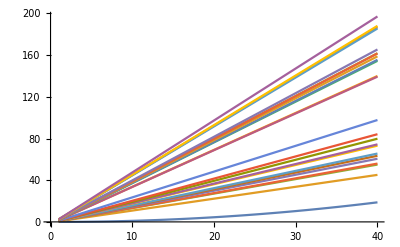

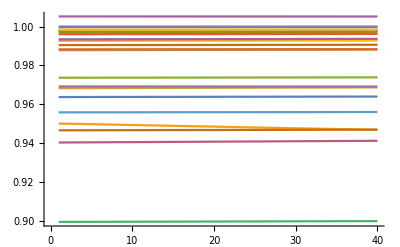

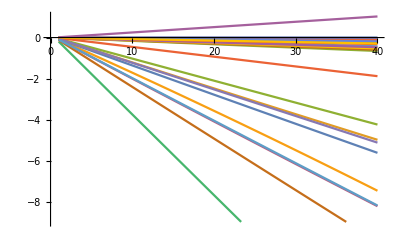

```mathematica
Plot the eigenvalues for all 24 bands;

(*Note the structure of 'fullEigenValues' is fullEigenValues[[order]][[band]][[eigenvalue]]*)

(*First 40 anharmonic eigenvalues of all 24 bands*)
ListPlot[Table[fullEigenValues[[1]][[i]],{i,1,24}],Joined->True]

(*First 40 anharmonic eigenvalues of all 24 bands divded by the harmonic values*)
ListPlot[Table[fullEigenValues[[2]][[i]]/fullEigenValues[[1]][[i]],{i,1,24}],Joined->True]

(*Anharmonic perturbation of eigenvalues - First 40 anharmonic eigenvalues of all 24 bands minus by the harmonic values*)
ListPlot[Table[fullEigenValues[[2]][[i]]-fullEigenValues[[1]][[i]],{i,1,24}],Joined->True]
```

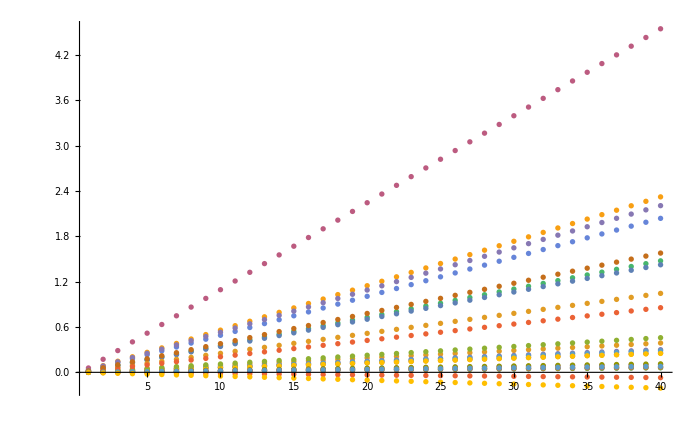

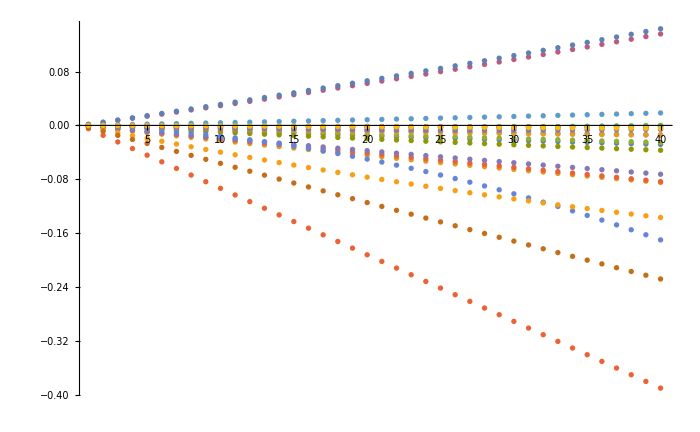

```mathematica
(*Anharmonic perturbation of occupation excitation spectrum*)
ListPlot[Table[Table[(fullEigenValues[[1]][[k]][[i]]/(omega0EigenValues[[k]][[1]]))-(-0.5+i),{i,1,maxEigenval}],{k,2,24}],PlotRange->All,ImageSize->700]
ListPlot[Table[Table[(fullEigenValues[[2]][[k]][[i]]/(omega0EigenValues[[k]][[1]]))-(-0.5+i),{i,1,maxEigenval}],{k,2,24}],PlotRange->All,ImageSize->700]
```

```mathematica
(*[[order]][[band]][[eigenvalue]]*)
(*[[band]][[1]]*)
Table[Table[(fullEigenValues[[1]][[k]][[i]]/(omega0EigenValues[[k]][[1]]))-(-0.5+i),{i,1,maxEigenval}],{k,2,24}]//TableForm
Table[Table[(fullEigenValues[[2]][[k]][[i]]/(omega0EigenValues[[k]][[1]]))-(-0.5+i),{i,1,maxEigenval}],{k,2,24}]//TableForm
```

0.00077473 | 0.00232419 | 0.00387365 | 0.00542311 | 0.00697257 | 0.00852203 | 0.0100715 | 0.011621 | 0.0131704 | 0.0147199 | 0.0162693 | 0.0178188 | 0.0193683 | 0.0209177 | 0.0224672 | 0.0240166 | 0.0255661 | 0.0271156 | 0.028665 | 0.0302145 | 0.0317639 | 0.0333134 | 0.0348629 | 0.0364123 | 0.0379618 | 0.0395112 | 0.0410607 | 0.0426102 | 0.0441596 | 0.0457091 | 0.0472585 | 0.048808 | 0.0503575 | 0.0519069 | 0.0534564 | 0.0550058 | 0.0565553 | 0.0581047 | 0.0596541 | 0.0612034
0.00491282 | 0.0147384 | 0.0245641 | 0.0343897 | 0.0442153 | 0.054041 | 0.0638666 | 0.0736922 | 0.0835179 | 0.0933435 | 0.103169 | 0.112995 | 0.12282 | 0.132646 | 0.142472 | 0.152297 | 0.162123 | 0.171949 | 0.181774 | 0.1916 | 0.201425 | 0.211251 | 0.221077 | 0.230902 | 0.240728 | 0.250554 | 0.260379 | 0.270205 | 0.280031 | 0.289856 | 0.299682 | 0.309507 | 0.319333 | 0.329159 | 0.338984 | 0.34881 | 0.358636 | 0.368461 | 0.378287 | 0.388112
0.000769487 | 0.00230846 | 0.00384743 | 0.00538641 | 0.00692538 | 0.00846436 | 0.0100033 | 0.0115423 | 0.0130813 | 0.0146203 | 0.0161592 | 0.0176982 | 0.0192372 | 0.0207761 | 0.0223151 | 0.0238541 | 0.0253931 | 0.026932 | 0.028471 | 0.03001 | 0.031549 | 0.0330879 | 0.0346269 | 0.0361659 | 0.0377049 | 0.0392438 | 0.0407828 | 0.0423218 | 0.0438608 | 0.0453997 | 0.0469387 | 0.0484777 | 0.0500167 | 0.0515556 | 0.0530946 | 0.0546336 | 0.0561726 | 0.0577115 | 0.0592505 | 0.0607895
-0.000893761 | -0.00268128 | -0.0044688 | -0.00625633 | -0.00804385 | -0.00983137 | -0.0116189 | -0.0134064 | -0.0151939 | -0.0169815 | -0.018769 | -0.0205565 | -0.022344 | -0.0241315 | -0.0259191 | -0.0277066 | -0.0294941 | -0.0312816 | -0.0330691 | -0.0348567 | -0.0366442 | -0.0384317 | -0.0402192 | -0.0420068 | -0.0437943 | -0.0455818 | -0.0473693 | -0.0491568 | -0.0509444 | -0.0527319 | -0.0545194 | -0.0563069 | -0.0580945 | -0.059882 | -0.0616695 | -0.063457 | -0.0652445 | -0.0670321 | -0.0688196 | -0.0706071
0.00379229 | 0.0113769 | 0.0189615 | 0.026546 | 0.0341306 | 0.0417152 | 0.0492998 | 0.0568844 | 0.064469 | 0.0720535 | 0.0796381 | 0.0872227 | 0.0948073 | 0.102392 | 0.109976 | 0.117561 | 0.125146 | 0.13273 | 0.140315 | 0.147899 | 0.155484 | 0.163069 | 0.170653 | 0.178238 | 0.185822 | 0.193407 | 0.200991 | 0.208576 | 0.216161 | 0.223745 | 0.23133 | 0.238914 | 0.246499 | 0.254084 | 0.261668 | 0.269253 | 0.276837 | 0.284422 | 0.292006 | 0.299591
0.00323797 | 0.00971391 | 0.0161898 | 0.0226658 | 0.0291417 | 0.0356177 | 0.0420936 | 0.0485695 | 0.0550455 | 0.0615214 | 0.0679974 | 0.0744733 | 0.0809492 | 0.0874252 | 0.0939011 | 0.100377 | 0.106853 | 0.113329 | 0.119805 | 0.126281 | 0.132757 | 0.139233 | 0.145709 | 0.152185 | 0.158661 | 0.165136 | 0.171612 | 0.178088 | 0.184564 | 0.19104 | 0.197516 | 0.203992 | 0.210468 | 0.216944 | 0.22342 | 0.229896 | 0.236372 | 0.242848 | 0.249324 | 0.2558
0.00361637 | 0.0108491 | 0.0180818 | 0.0253146 | 0.0325473 | 0.0397801 | 0.0470128 | 0.0542455 | 0.0614783 | 0.068711 | 0.0759437 | 0.0831765 | 0.0904092 | 0.0976419 | 0.104875 | 0.112107 | 0.11934 | 0.126573 | 0.133806 | 0.141038 | 0.148271 | 0.155504 | 0.162737 | 0.169969 | 0.177202 | 0.184435 | 0.191668 | 0.1989 | 0.206133 | 0.213366 | 0.220598 | 0.227831 | 0.235064 | 0.242297 | 0.249529 | 0.256762 | 0.263995 | 0.271228 | 0.27846 | 0.285693
0.00317116 | 0.00951347 | 0.0158558 | 0.0221981 | 0.0285404 | 0.0348827 | 0.041225 | 0.0475673 | 0.0539097 | 0.060252 | 0.0665943 | 0.0729366 | 0.0792789 | 0.0856212 | 0.0919635 | 0.0983059 | 0.104648 | 0.11099 | 0.117333 | 0.123675 | 0.130017 | 0.13636 | 0.142702 | 0.149044 | 0.155387 | 0.161729 | 0.168071 | 0.174414 | 0.180756 | 0.187098 | 0.193441 | 0.199783 | 0.206125 | 0.212467 | 0.21881 | 0.225152 | 0.231494 | 0.237837 | 0.244179 | 0.250521
0.00130579 | 0.00391736 | 0.00652894 | 0.00914052 | 0.0117521 | 0.0143637 | 0.0169752 | 0.0195868 | 0.0221984 | 0.02481 | 0.0274216 | 0.0300331 | 0.0326447 | 0.0352563 | 0.0378679 | 0.0404794 | 0.043091 | 0.0457026 | 0.0483142 | 0.0509257 | 0.0535373 | 0.0561489 | 0.0587605 | 0.0613721 | 0.0639836 | 0.0665952 | 0.0692068 | 0.0718184 | 0.0744299 | 0.0770415 | 0.0796531 | 0.0822647 | 0.0848762 | 0.0874878 | 0.0900994 | 0.092711 | 0.0953226 | 0.0979341 | 0.100546 | 0.103157
0.00141814 | 0.00425442 | 0.00709071 | 0.00992699 | 0.0127633 | 0.0155996 | 0.0184358 | 0.0212721 | 0.0241084 | 0.0269447 | 0.029781 | 0.0326172 | 0.0354535 | 0.0382898 | 0.0411261 | 0.0439624 | 0.0467987 | 0.0496349 | 0.0524712 | 0.0553075 | 0.0581438 | 0.0609801 | 0.0638164 | 0.0666526 | 0.0694889 | 0.0723252 | 0.0751615 | 0.0779978 | 0.0808341 | 0.0836703 | 0.0865066 | 0.0893429 | 0.0921792 | 0.0950155 | 0.0978517 | 0.100688 | 0.103524 | 0.106361 | 0.109197 | 0.112033
0.000929741 | 0.00278922 | 0.00464871 | 0.00650819 | 0.00836767 | 0.0102272 | 0.0120866 | 0.0139461 | 0.0158056 | 0.0176651 | 0.0195246 | 0.0213841 | 0.0232435 | 0.025103 | 0.0269625 | 0.028822 | 0.0306815 | 0.0325409 | 0.0344004 | 0.0362599 | 0.0381194 | 0.0399789 | 0.0418384 | 0.0436978 | 0.0455573 | 0.0474168 | 0.0492763 | 0.0511358 | 0.0529953 | 0.0548547 | 0.0567142 | 0.0585737 | 0.0604332 | 0.0622927 | 0.0641522 | 0.0660116 | 0.0678711 | 0.0697306 | 0.0715901 | 0.0734496
0.0258079 | 0.0774236 | 0.129039 | 0.180655 | 0.232271 | 0.283887 | 0.335502 | 0.387118 | 0.438734 | 0.49035 | 0.541965 | 0.593581 | 0.645197 | 0.696813 | 0.748429 | 0.800044 | 0.85166 | 0.903276 | 0.954892 | 1.00651 | 1.05812 | 1.10974 | 1.16135 | 1.21297 | 1.26459 | 1.3162 | 1.36782 | 1.41943 | 1.47105 | 1.52266 | 1.57428 | 1.6259 | 1.67751 | 1.72913 | 1.78074 | 1.83236 | 1.88398 | 1.93559 | 1.98721 | 2.03882
0.0294074 | 0.0882222 | 0.147037 | 0.205852 | 0.264667 | 0.323481 | 0.382296 | 0.441111 | 0.499926 | 0.558741 | 0.617555 | 0.67637 | 0.735185 | 0.794 | 0.852815 | 0.911629 | 0.970444 | 1.02926 | 1.08807 | 1.14689 | 1.2057 | 1.26452 | 1.32333 | 1.38215 | 1.44096 | 1.49978 | 1.55859 | 1.61741 | 1.67622 | 1.73504 | 1.79385 | 1.85267 | 1.91148 | 1.9703 | 2.02911 | 2.08793 | 2.14674 | 2.20555 | 2.26437 | 2.32318
0.0575819 | 0.172746 | 0.28791 | 0.403074 | 0.518237 | 0.633401 | 0.748565 | 0.863729 | 0.978893 | 1.09406 | 1.20922 | 1.32438 | 1.43955 | 1.55471 | 1.66988 | 1.78504 | 1.9002 | 2.01537 | 2.13053 | 2.2457 | 2.36086 | 2.47602 | 2.59119 | 2.70635 | 2.82151 | 2.93668 | 3.05184 | 3.16701 | 3.28217 | 3.39733 | 3.5125 | 3.62766 | 3.74283 | 3.85799 | 3.97315 | 4.08832 | 4.20348 | 4.31865 | 4.43381 | 4.54897
0.0186836 | 0.0560508 | 0.0934181 | 0.130785 | 0.168153 | 0.20552 | 0.242887 | 0.280254 | 0.317621 | 0.354989 | 0.392356 | 0.429723 | 0.46709 | 0.504458 | 0.541825 | 0.579192 | 0.616559 | 0.653926 | 0.691294 | 0.728661 | 0.766028 | 0.803395 | 0.840763 | 0.87813 | 0.915497 | 0.952864 | 0.990231 | 1.0276 | 1.06497 | 1.10233 | 1.1397 | 1.17707 | 1.21443 | 1.2518 | 1.28917 | 1.32654 | 1.3639 | 1.40127 | 1.43864 | 1.47601
0.0180248 | 0.0540744 | 0.0901239 | 0.126174 | 0.162223 | 0.198273 | 0.234322 | 0.270372 | 0.306421 | 0.342471 | 0.378521 | 0.41457 | 0.45062 | 0.486669 | 0.522719 | 0.558768 | 0.594818 | 0.630868 | 0.666917 | 0.702967 | 0.739016 | 0.775066 | 0.811115 | 0.847165 | 0.883215 | 0.919264 | 0.955314 | 0.991363 | 1.02741 | 1.06346 | 1.09951 | 1.13556 | 1.17161 | 1.20766 | 1.24371 | 1.27976 | 1.31581 | 1.35186 | 1.38791 | 1.42396
0.0132319 | 0.0396957 | 0.0661596 | 0.0926234 | 0.119087 | 0.145551 | 0.172015 | 0.198479 | 0.224943 | 0.251406 | 0.27787 | 0.304334 | 0.330798 | 0.357262 | 0.383726 | 0.410189 | 0.436653 | 0.463117 | 0.489581 | 0.516045 | 0.542508 | 0.568972 | 0.595436 | 0.6219 | 0.648364 | 0.674828 | 0.701291 | 0.727755 | 0.754219 | 0.780683 | 0.807147 | 0.833611 | 0.860074 | 0.886538 | 0.913002 | 0.939466 | 0.96593 | 0.992394 | 1.01886 | 1.04532
0.00580399 | 0.017412 | 0.0290199 | 0.0406279 | 0.0522359 | 0.0638439 | 0.0754519 | 0.0870598 | 0.0986678 | 0.110276 | 0.121884 | 0.133492 | 0.1451 | 0.156708 | 0.168316 | 0.179924 | 0.191532 | 0.20314 | 0.214748 | 0.226356 | 0.237964 | 0.249572 | 0.261179 | 0.272787 | 0.284395 | 0.296003 | 0.307611 | 0.319219 | 0.330827 | 0.342435 | 0.354043 | 0.365651 | 0.377259 | 0.388867 | 0.400475 | 0.412083 | 0.423691 | 0.435299 | 0.446907 | 0.458515
0.0108322 | 0.0324966 | 0.054161 | 0.0758254 | 0.0974898 | 0.119154 | 0.140819 | 0.162483 | 0.184147 | 0.205812 | 0.227476 | 0.24914 | 0.270805 | 0.292469 | 0.314134 | 0.335798 | 0.357462 | 0.379127 | 0.400791 | 0.422456 | 0.44412 | 0.465784 | 0.487449 | 0.509113 | 0.530778 | 0.552442 | 0.574106 | 0.595771 | 0.617435 | 0.6391 | 0.660764 | 0.682428 | 0.704093 | 0.725757 | 0.747421 | 0.769086 | 0.79075 | 0.812415 | 0.834079 | 0.855743
0.0279381 | 0.0838142 | 0.13969 | 0.195567 | 0.251443 | 0.307319 | 0.363195 | 0.419071 | 0.474947 | 0.530823 | 0.5867 | 0.642576 | 0.698452 | 0.754328 | 0.810204 | 0.86608 | 0.921957 | 0.977833 | 1.03371 | 1.08959 | 1.14546 | 1.20134 | 1.25721 | 1.31309 | 1.36897 | 1.42484 | 1.48072 | 1.53659 | 1.59247 | 1.64835 | 1.70422 | 1.7601 | 1.81598 | 1.87185 | 1.92773 | 1.9836 | 2.03948 | 2.09536 | 2.15123 | 2.20711
0.019988 | 0.0599641 | 0.0999401 | 0.139916 | 0.179892 | 0.219868 | 0.259844 | 0.29982 | 0.339796 | 0.379772 | 0.419749 | 0.459725 | 0.499701 | 0.539677 | 0.579653 | 0.619629 | 0.659605 | 0.699581 | 0.739557 | 0.779533 | 0.819509 | 0.859485 | 0.899461 | 0.939437 | 0.979413 | 1.01939 | 1.05937 | 1.09934 | 1.13932 | 1.17929 | 1.21927 | 1.25925 | 1.29922 | 1.3392 | 1.37917 | 1.41915 | 1.45913 | 1.4991 | 1.53908 | 1.57905
0.00100368 | 0.00301105 | 0.00501841 | 0.00702577 | 0.00903314 | 0.0110405 | 0.0130479 | 0.0150552 | 0.0170626 | 0.01907 | 0.0210773 | 0.0230847 | 0.025092 | 0.0270994 | 0.0291068 | 0.0311141 | 0.0331215 | 0.0351289 | 0.0371362 | 0.0391436 | 0.041151 | 0.0431583 | 0.0451657 | 0.047173 | 0.0491804 | 0.0511878 | 0.0531951 | 0.0552025 | 0.0572099 | 0.0592172 | 0.0612246 | 0.063232 | 0.0652393 | 0.0672467 | 0.069254 | 0.0712614 | 0.0732688 | 0.0752761 | 0.0772835 | 0.0792909
-0.0026424 | -0.00792721 | -0.013212 | -0.0184968 | -0.0237816 | -0.0290664 | -0.0343513 | -0.0396361 | -0.0449209 | -0.0502057 | -0.0554905 | -0.0607753 | -0.0660601 | -0.0713449 | -0.0766297 | -0.0819145 | -0.0871993 | -0.0924841 | -0.097769 | -0.103054 | -0.108339 | -0.113623 | -0.118908 | -0.124193 | -0.129478 | -0.134763 | -0.140047 | -0.145332 | -0.150617 | -0.155902 | -0.161187 | -0.166471 | -0.171756 | -0.177041 | -0.182326 | -0.187611 | -0.192896 | -0.19818 | -0.203465 | -0.20875

-0.000419915 | -0.0012564 | -0.0020862 | -0.00290933 | -0.00372582 | -0.00453568 | -0.00533893 | -0.00613559 | -0.00692568 | -0.00770922 | -0.00848622 | -0.00925671 | -0.0100207 | -0.0107782 | -0.0115293 | -0.0122739 | -0.013012 | -0.0137438 | -0.0144692 | -0.0151882 | -0.0159009 | -0.0166072 | -0.0173072 | -0.0180009 | -0.0186883 | -0.0193695 | -0.0200444 | -0.0207131 | -0.0213756 | -0.0220319 | -0.022682 | -0.0233259 | -0.0239637 | -0.0245954 | -0.025221 | -0.0258404 | -0.0264538 | -0.0270612 | -0.0276626 | -0.0282581
-0.00121064 | -0.00362466 | -0.00602419 | -0.00840922 | -0.0107798 | -0.0131358 | -0.0154774 | -0.0178045 | -0.0201171 | -0.0224153 | -0.024699 | -0.0269683 | -0.0292231 | -0.0314635 | -0.0336895 | -0.035901 | -0.038098 | -0.0402807 | -0.042449 | -0.0446028 | -0.0467422 | -0.0488673 | -0.0509779 | -0.0530741 | -0.055156 | -0.0572235 | -0.0592766 | -0.0613153 | -0.0633396 | -0.0653496 | -0.0673453 | -0.0693266 | -0.0712935 | -0.0732461 | -0.0751844 | -0.0771083 | -0.0790179 | -0.0809132 | -0.0827941 | -0.0846608
-0.000351187 | -0.00105195 | -0.00174949 | -0.00244382 | -0.00313493 | -0.00382284 | -0.00450756 | -0.00518908 | -0.00586741 | -0.00654257 | -0.00721455 | -0.00788335 | -0.008549 | -0.00921148 | -0.00987081 | -0.010527 | -0.01118 | -0.0118299 | -0.0124767 | -0.0131204 | -0.0137609 | -0.0143983 | -0.0150326 | -0.0156638 | -0.0162919 | -0.0169169 | -0.0175388 | -0.0181576 | -0.0187734 | -0.019386 | -0.0199957 | -0.0206022 | -0.0212057 | -0.0218061 | -0.0224035 | -0.0229979 | -0.0235892 | -0.0241775 | -0.0247627 | -0.025345
-0.00105142 | -0.00315452 | -0.00525818 | -0.00736237 | -0.00946712 | -0.0115724 | -0.0136782 | -0.0157846 | -0.0178916 | -0.0199991 | -0.0221071 | -0.0242157 | -0.0263249 | -0.0284346 | -0.0305448 | -0.0326557 | -0.0347671 | -0.036879 | -0.0389915 | -0.0411046 | -0.0432182 | -0.0453324 | -0.0474471 | -0.0495624 | -0.0516783 | -0.0537948 | -0.0559118 | -0.0580294 | -0.0601475 | -0.0622663 | -0.0643856 | -0.0665054 | -0.0686259 | -0.0707469 | -0.0728685 | -0.0749907 | -0.0771134 | -0.0792367 | -0.0813606 | -0.0834851
-0.00100246 | -0.00300305 | -0.004995 | -0.00697829 | -0.0089529 | -0.0109188 | -0.012876 | -0.0148244 | -0.0167641 | -0.0186951 | -0.0206172 | -0.0225305 | -0.024435 | -0.0263306 | -0.0282174 | -0.0300953 | -0.0319643 | -0.0338244 | -0.0356755 | -0.0375177 | -0.0393509 | -0.0411752 | -0.0429904 | -0.0447966 | -0.0465938 | -0.0483819 | -0.050161 | -0.0519309 | -0.0536918 | -0.0554435 | -0.0571861 | -0.0589196 | -0.0606438 | -0.0623589 | -0.0640648 | -0.0657615 | -0.0674489 | -0.0691271 | -0.070796 | -0.0724557
-0.0000735217 | -0.000218115 | -0.000357808 | -0.000492602 | -0.000622496 | -0.000747489 | -0.00086758 | -0.00098277 | -0.00109306 | -0.00119844 | -0.00129892 | -0.0013945 | -0.00148517 | -0.00157094 | -0.0016518 | -0.00172776 | -0.00179881 | -0.00186495 | -0.00192618 | -0.00198251 | -0.00203392 | -0.00208043 | -0.00212202 | -0.00215871 | -0.00219048 | -0.00221734 | -0.00223929 | -0.00225632 | -0.00226844 | -0.00227564 | -0.00227793 | -0.0022753 | -0.00226775 | -0.00225529 | -0.0022379 | -0.0022156 | -0.00218838 | -0.00215623 | -0.00211917 | -0.00207718
-0.0000849129 | -0.000251207 | -0.000410441 | -0.000562618 | -0.000707743 | -0.000845817 | -0.000976847 | -0.00110083 | -0.00121778 | -0.00132769 | -0.00143058 | -0.00152643 | -0.00161526 | -0.00169707 | -0.00177186 | -0.00183963 | -0.0019004 | -0.00195415 | -0.00200091 | -0.00204066 | -0.00207342 | -0.00209918 | -0.00211796 | -0.00212974 | -0.00213455 | -0.00213237 | -0.00212322 | -0.0021071 | -0.002084 | -0.00205394 | -0.00201692 | -0.00197293 | -0.00192199 | -0.0018641 | -0.00179926 | -0.00172747 | -0.00164874 | -0.00156307 | -0.00147046 | -0.00137092
-0.000177537 | -0.00052294 | -0.00084903 | -0.00115586 | -0.00144348 | -0.00171195 | -0.00196131 | -0.00219161 | -0.00240291 | -0.00259527 | -0.00276872 | -0.00292332 | -0.00305913 | -0.00317619 | -0.00327455 | -0.00335427 | -0.00341539 | -0.00345797 | -0.00348205 | -0.00348768 | -0.00347493 | -0.00344382 | -0.00339443 | -0.00332678 | -0.00324094 | -0.00313695 | -0.00301487 | -0.00287473 | -0.0027166 | -0.00254052 | -0.00234653 | -0.00213469 | -0.00190505 | -0.00165765 | -0.00139254 | -0.00110977 | -0.000809393 | -0.00049145 | -0.00015599 | 0.000196938
-0.000202585 | -0.000606487 | -0.00100786 | -0.0014067 | -0.00180301 | -0.00219681 | -0.00258809 | -0.00297686 | -0.00336312 | -0.00374688 | -0.00412814 | -0.00450691 | -0.00488319 | -0.00525698 | -0.00562829 | -0.00599713 | -0.00636349 | -0.00672738 | -0.00708881 | -0.00744778 | -0.00780429 | -0.00815835 | -0.00850996 | -0.00885912 | -0.00920585 | -0.00955014 | -0.009892 | -0.0102314 | -0.0105684 | -0.010903 | -0.0112352 | -0.011565 | -0.0118923 | -0.0122173 | -0.0125398 | -0.01286 | -0.0131777 | -0.0134931 | -0.0138061 | -0.0141167
-0.000545204 | -0.00163146 | -0.00270943 | -0.00377913 | -0.00484057 | -0.00589377 | -0.00693875 | -0.00797553 | -0.00900413 | -0.0100245 | -0.0110368 | -0.012041 | -0.013037 | -0.0140249 | -0.0150047 | -0.0159765 | -0.0169402 | -0.0178959 | -0.0188436 | -0.0197832 | -0.0207149 | -0.0216387 | -0.0225544 | -0.0234623 | -0.0243622 | -0.0252542 | -0.0261384 | -0.0270147 | -0.0278831 | -0.0287437 | -0.0295965 | -0.0304414 | -0.0312786 | -0.0321081 | -0.0329297 | -0.0337437 | -0.0345499 | -0.0353484 | -0.0361393 | -0.0369224
-0.0000459167 | -0.000136943 | -0.000226356 | -0.000314158 | -0.000400348 | -0.000484929 | -0.000567902 | -0.000649267 | -0.000729026 | -0.00080718 | -0.00088373 | -0.000958676 | -0.00103202 | -0.00110376 | -0.00117391 | -0.00124245 | -0.0013094 | -0.00137475 | -0.00143851 | -0.00150067 | -0.00156123 | -0.00162021 | -0.00167759 | -0.00173339 | -0.00178759 | -0.00184021 | -0.00189124 | -0.00194068 | -0.00198854 | -0.00203481 | -0.0020795 | -0.00212261 | -0.00216414 | -0.00220409 | -0.00224246 | -0.00227925 | -0.00231447 | -0.00234811 | -0.00238018 | -0.00241067
-0.000453613 | -0.0014518 | -0.00263168 | -0.00399283 | -0.0055348 | -0.00725715 | -0.00915945 | -0.0112413 | -0.0135021 | -0.0159416 | -0.0185593 | -0.0213547 | -0.0243274 | -0.027477 | -0.030803 | -0.0343049 | -0.0379825 | -0.0418351 | -0.0458623 | -0.0500638 | -0.0544391 | -0.0589877 | -0.0637091 | -0.068603 | -0.073669 | -0.0789064 | -0.0843151 | -0.0898943 | -0.0956438 | -0.101563 | -0.107652 | -0.113909 | -0.120335 | -0.126929 | -0.133691 | -0.14062 | -0.147715 | -0.154977 | -0.162404 | -0.169997
-0.00219407 | -0.00655803 | -0.0108736 | -0.0151409 | -0.0193598 | -0.0235305 | -0.0276528 | -0.031727 | -0.0357528 | -0.0397305 | -0.0436599 | -0.0475412 | -0.0513743 | -0.0551592 | -0.0588961 | -0.0625848 | -0.0662254 | -0.069818 | -0.0733625 | -0.0768591 | -0.0803076 | -0.0837081 | -0.0870606 | -0.0903652 | -0.0936219 | -0.0968307 | -0.0999915 | -0.103105 | -0.10617 | -0.109187 | -0.112157 | -0.115078 | -0.117952 | -0.120778 | -0.123557 | -0.126288 | -0.128971 | -0.131606 | -0.134194 | -0.136734
0.00149347 | 0.00449163 | 0.00751228 | 0.0105555 | 0.0136214 | 0.01671 | 0.0198214 | 0.0229556 | 0.0261129 | 0.0292932 | 0.0324966 | 0.0357232 | 0.0389731 | 0.0422464 | 0.0455431 | 0.0488633 | 0.0522071 | 0.0555746 | 0.0589658 | 0.0623808 | 0.0658197 | 0.0692827 | 0.0727696 | 0.0762807 | 0.0798161 | 0.0833757 | 0.0869596 | 0.090568 | 0.0942009 | 0.0978584 | 0.101541 | 0.105248 | 0.108979 | 0.112736 | 0.116517 | 0.120324 | 0.124156 | 0.128013 | 0.131895 | 0.135803
-0.000132194 | -0.000389956 | -0.000634465 | -0.000865719 | -0.00108372 | -0.00128846 | -0.00147994 | -0.00165816 | -0.00182311 | -0.00197481 | -0.00211323 | -0.0022384 | -0.00235029 | -0.00244891 | -0.00253426 | -0.00260634 | -0.00266514 | -0.00271067 | -0.00274291 | -0.00276188 | -0.00276757 | -0.00275998 | -0.0027391 | -0.00270494 | -0.00265749 | -0.00259675 | -0.00252272 | -0.0024354 | -0.00233479 | -0.00222088 | -0.00209368 | -0.00195318 | -0.00179938 | -0.00163228 | -0.00145187 | -0.00125817 | -0.00105116 | -0.000830837 | -0.000597211 | -0.000350274
0.00158793 | 0.00477578 | 0.00798757 | 0.0112233 | 0.0144829 | 0.0177664 | 0.0210737 | 0.0244049 | 0.0277599 | 0.0311387 | 0.0345413 | 0.0379677 | 0.0414178 | 0.0448916 | 0.0483891 | 0.0519102 | 0.0554551 | 0.0590235 | 0.0626156 | 0.0662313 | 0.0698706 | 0.0735334 | 0.0772197 | 0.0809296 | 0.084663 | 0.0884198 | 0.0922001 | 0.0960038 | 0.099831 | 0.103681 | 0.107555 | 0.111453 | 0.115373 | 0.119317 | 0.123284 | 0.127275 | 0.131289 | 0.135326 | 0.139386 | 0.143469
-0.000282566 | -0.000842489 | -0.00139199 | -0.00193108 | -0.00245975 | -0.00297799 | -0.00348582 | -0.00398323 | -0.00447022 | -0.00494679 | -0.00541294 | -0.00586867 | -0.00631398 | -0.00674887 | -0.00717333 | -0.00758738 | -0.007991 | -0.0083842 | -0.00876698 | -0.00913934 | -0.00950128 | -0.00985279 | -0.0101939 | -0.0105245 | -0.0108448 | -0.0111546 | -0.011454 | -0.011743 | -0.0120215 | -0.0122896 | -0.0125473 | -0.0127946 | -0.0130315 | -0.0132579 | -0.0134739 | -0.0136794 | -0.0138746 | -0.0140593 | -0.0142336 | -0.0143975
-0.000113064 | -0.000336828 | -0.000555866 | -0.000770177 | -0.00097976 | -0.00118461 | -0.00138474 | -0.00158013 | -0.00177079 | -0.00195672 | -0.00213791 | -0.00231436 | -0.00248609 | -0.00265307 | -0.00281532 | -0.00297282 | -0.00312559 | -0.00327362 | -0.0034169 | -0.00355544 | -0.00368924 | -0.00381829 | -0.0039426 | -0.00406216 | -0.00417697 | -0.00428703 | -0.00439235 | -0.00449291 | -0.00458872 | -0.00467978 | -0.00476609 | -0.00484764 | -0.00492444 | -0.00499648 | -0.00506376 | -0.00512629 | -0.00518406 | -0.00523706 | -0.00528531 | -0.00532879
-0.0049121 | -0.0147379 | -0.024567 | -0.0343992 | -0.0442345 | -0.054073 | -0.0639144 | -0.0737589 | -0.0836062 | -0.0934565 | -0.10331 | -0.113166 | -0.123024 | -0.132886 | -0.14275 | -0.152616 | -0.162486 | -0.172357 | -0.182231 | -0.192108 | -0.201987 | -0.211869 | -0.221752 | -0.231638 | -0.241526 | -0.251416 | -0.261309 | -0.271203 | -0.2811 | -0.290998 | -0.300899 | -0.310801 | -0.320705 | -0.330611 | -0.340518 | -0.350428 | -0.360339 | -0.370251 | -0.380166 | -0.390081
-0.000268022 | -0.00079384 | -0.00129921 | -0.00178413 | -0.00224861 | -0.00269264 | -0.00311622 | -0.00351937 | -0.00390207 | -0.00426432 | -0.00460614 | -0.00492752 | -0.00522846 | -0.00550896 | -0.00576902 | -0.00600865 | -0.00622784 | -0.0064266 | -0.00660493 | -0.00676282 | -0.00690028 | -0.00701732 | -0.00711392 | -0.00719009 | -0.00724584 | -0.00728116 | -0.00729606 | -0.00729053 | -0.00726458 | -0.0072182 | -0.0071514 | -0.00706419 | -0.00695655 | -0.00682849 | -0.00668002 | -0.00651113 | -0.00632183 | -0.0061121 | -0.00588197 | -0.00563142
-0.00298472 | -0.00894917 | -0.0149036 | -0.020848 | -0.0267823 | -0.0327066 | -0.0386208 | -0.0445249 | -0.0504189 | -0.0563028 | -0.0621766 | -0.0680402 | -0.0738937 | -0.079737 | -0.0855702 | -0.0913931 | -0.0972059 | -0.103008 | -0.108801 | -0.114583 | -0.120354 | -0.126116 | -0.131867 | -0.137608 | -0.143339 | -0.149059 | -0.154769 | -0.160469 | -0.166158 | -0.171837 | -0.177505 | -0.183163 | -0.188811 | -0.194448 | -0.200075 | -0.205691 | -0.211297 | -0.216893 | -0.222477 | -0.228052
0.000199984 | 0.000601751 | 0.00100711 | 0.00141607 | 0.00182861 | 0.00224473 | 0.00266443 | 0.0030877 | 0.00351454 | 0.00394495 | 0.00437891 | 0.00481644 | 0.00525751 | 0.00570213 | 0.0061503 | 0.006602 | 0.00705724 | 0.00751601 | 0.00797831 | 0.00844412 | 0.00891346 | 0.00938631 | 0.00986266 | 0.0103425 | 0.0108259 | 0.0113127 | 0.0118031 | 0.0122969 | 0.0127943 | 0.0132951 | 0.0137993 | 0.0143071 | 0.0148183 | 0.015333 | 0.0158511 | 0.0163727 | 0.0168977 | 0.0174262 | 0.0179581 | 0.0184935
-0.0000412815 | -0.000124551 | -0.000209234 | -0.000295331 | -0.000382842 | -0.000471768 | -0.000562107 | -0.000653861 | -0.000747029 | -0.000841612 | -0.00093761 | -0.00103502 | -0.00113385 | -0.00123409 | -0.00133575 | -0.00143883 | -0.00154332 | -0.00164922 | -0.00175654 | -0.00186528 | -0.00197543 | -0.002087 | -0.00219999 | -0.00231439 | -0.00243021 | -0.00254745 | -0.0026661 | -0.00278618 | -0.00290766 | -0.00303057 | -0.00315489 | -0.00328064 | -0.00340779 | -0.00353637 | -0.00366637 | -0.00379778 | -0.00393061 | -0.00406486 | -0.00420053 | -0.00433762

```mathematica
(*[[order]][[band]][[eigenvalue]]*)
(*[[band]][[1]]*)
fullEigenValues[[1]][[24]]
omega0EigenValues[[2]][[1]]
```

{2.49473,7.4842,12.4737,17.4631,22.4526,27.4421,32.4315,37.421,42.4105,47.3999,52.3894,57.3789,62.3683,67.3578,72.3473,77.3367,82.3262,87.3157,92.3051,97.2946,102.284,107.274,112.263,117.252,122.242,127.231,132.221,137.21,142.2,147.189,152.179,157.168,162.158,167.147,172.137,177.126,182.116,187.105,192.094,197.084}

1.14018

```mathematica
Partition function;
(*Make partition function as function of temperature*)
(* 1/Z * e^-beta*E *)

(*Zirconium partition function*)
zrperfectHarmonicZ[T_]:=Total[Exp[-(zOmega0*perfectHarmonic)/(kB*T)]]
zr12thfitZ[T_]:=Total[Exp[-(zOmega0*eigenEnergiesZ[[6]])/(kB*T)]]
(*Carbon partition function*)
cperfectHarmonicZ[T_]:=Total[Exp[-(cOmega0*perfectHarmonic)/(kB*T)]]
c12thfitZ[T_]:=Total[Exp[-(cOmega0*eigenEnergies[[6]])/(kB*T)]]
```